# 1. Ordinary Differential Equations in the Physical Sciences

## 1.1 Introduction

1.1.1 Definitions

## Differential Equations, Unknown Functions, and Initial Conditions

Three centuries ago, the great British prodigy  Sir Isaac Newton  and the German mathematician Gottfried von Liebniz independently introduced the world to calculus, and thereby ushered in the modern scientific era. It has since been established in countless experiments that natural phenomena of all kinds can be described, often in exquisite detail, by the solutions to differential equations.

Differential equations involve derivatives of an unknown function whose form is determined through solution of the equations. For example, consider the motion (in one dimension) of a point particle of mass m under the action of a prescribed time-dependent force F(t). The particle's velocity v(t) satisfies Newton's second law

m ⅆv/ⅆt = F(t).

This is a differential equation for the unknown function v(t).

Equation (1.1.1) is probably the simplest differential equation that one can write down. It can be solved by applying the fundamental theorem of calculus:  for any function f(t) whose derivative exists and is integrable on the interval [a,b],

∫_a^b ⅆf/ⅆt ⅆt=f(b)-f(a).

Integrating both sides of Eq. (1.1.1) from an initial time t=0 to time t and using Eq. (1.1.2) yields

∫_0^t (ⅆ v)/ⅆt ⅆt=v(t)-v(0)=1/m∫_0^t F(t)ⅆt.

Therefore, the solution of Eq. (1.1.1) for the velocity at time t is given by the integral over time of the force, a known function, and an initial condition, the velocity at time t=0. This initial condition can be thought of mathematically as a constant of integration that appears when the integral is applied to Eq. (1.1.1).  Physically,  the requirement that we need to know the initial velocity in order to find the velocity at later times is intuitively obvious.  However, it also implies that the differential equation (1.1.1) by itself is not enough to completely determine a solution for v(t); the initial velocity must also be provided. This is a general feature of differential equations:

Extra conditions beyond the equation itself must be supplied in order to completely determine a solution of a differential equation.

If the initial condition is not  known, so that v(0) is an undetermined constant in Eq. (1.1.3), then we call Eq. (1.1.3) a general solution to the differential equation, because different choices of the undetermined constant allow the solution to satisfy different initial conditions.

As a second example of a differential equation, let's now assume that the force in Eq. (1.1.1) depends on the position x(t) of the particle according to Hooke's law:

F(t) = - k x(t),

where k is a constant (the spring constant). Then, using the definition of velocity as the rate of change of position,

v=ⅆx/ⅆt.

Eq. (1.1.1) becomes a differential equation for the unknown function x(t):

(ⅆ^2 x)/(ⅆ t^2)=-k/mx(t).

This familiar differential equation, the harmonic oscillator equation, has a general solution in terms of the trigonometric functions sin x and cos x, and two undetermined constants C_1 and C_2:

x(t)=C_1 cos(ω_o t) +C_2 sin(ω_o t),

where  ω_o=√(k/m) is the natural frequency of the oscillation.  The two constants can be determined by two initial conditions, on the initial position and velocity:

x(0) = x_o , v(0)=v_o.

Since Eq. (1.1.7) implies that x(0) = C_1 and  x'(0)=v(0)=ω_o C_2, the solution can be written directly in terms of the initial conditions as

x(t)=x_o cos(ω_o t) +v_o/ω_o sin(ω_o t).

We can easily verify that this solution satisfies the differential equation by substituting it into  Eq. (1.1.6):

```mathematica
x[t_] = x0 Cos[Subscript[ω, o] t] + v0/Subscript[ω, o] Sin[Subscript[ω, o]  t];
Simplify[ x''[t] == -Subscript[ω, o]^2 x[t]]
```

True

We can also verify that the solution matches the initial conditions:

```mathematica
x[0]
```

x0

```mathematica
x'[0]
```

v0

## Order of a Differential Equation

The order of a differential equation is the order of the highest derivative of the unknown function that appears in the equation. Since only a first derivative of v(t)  appears in Eq. (1.1.1), the equation is a  first-order differential equation for v(t). On the other hand, Equation (1.1.6) is a second-order differential equation.

Note that the general solution (1.1.3) of the first-order equation (1.1.1) involved one undetermined constant, but for the second-order equation, two undetermined constants were required in  Eq. (1.1.7). It's easy to see why this must be so - an Nth-order differential equation involves the Nth derivative of the unknown function. To determine this function one needs to integrate the equation N times, giving N constants of integration.

The number of undetermined constants that enter the general solution of an ordinary differential equation equals the order of the equation.

## Partial Differential Equations

The above statement applies only to ordinary differential equations (ODEs), which are differential equations for which derivatives of the unknown function are taken with respect to only a single variable.  The two examples that we have seen so far have been ODEs, since only derivatives with respect to time appeared. However, this book will also consider partial differential equations (PDEs), which involve derivatives of the unknown function with respect to several variables.  One example of a PDE is Poisson's equation, relating the electrostatic potential ϕ(x,y,z) to the charge density ρ(x,y,z) of a distribution of charges:

∇^2 ϕ(x,y,z)=-(ρ(x,y,z))/ϵ_o.

Here ϵ_o is a constant (the dielectric permittivity of free space, given by  ϵ_o=8.85... ×10^-12F/m), and ∇^2  is the Laplacian operator,

∇^2 =∂^2/(∂x^2)+∂^2/(∂y^2)+∂^2/(∂z^2).

We will find that  ∇^2  appears frequently in the equations of mathematical physics.

Like ODEs, PDEs must be supplemented with extra conditions in order to obtain a specific solution. However, the form of these conditions becomes more complex than for ODEs. In the case of Poisson's equation,  boundary conditions must be specified over one or more surfaces that bound the volume within which the solution for ϕ(x,y,z) is determined.

A discussion of solutions to Poisson’s equation and other PDE’s of mathematical physics can be found in Chapter 3 and later chapters. For now we will confine ourselves to ODEs. Many of the techniques used to solve ODEs can also be applied to PDEs.

An ODE involves derivatives of the unknown function with respect to only a single variable. A PDE involves derivatives of the unknown function with respect to more than one variable.

## Initial-Value and Boundary-Value Problems

Even if we limit discussion to ODEs, there is still an important distinction to be made, between initial-value problems and boundary-value problems. In initial-value problems, the unknown function is required in some time domain t >0 and all conditions to specify  the solution are given at one end of this domain, at t =0. Equations (1.1.3) and (1.1.9) are solutions of initial-value problems.

However, in boundary-value problems, conditions that specify the solution are given at different times or places. Examples of boundary-value problems in ODEs may be found in Sec. 1.5. (Problems involving PDE’s are often boundary- value problems; Poisson’s equation (1.1.10) is an example. In Chapter 3 we will find that some PDE’s involving both time and space derivatives are solved as both boundary- and initial-value problems.)

For now, we will stick to a discussion of ODE initial-value problems.

In initial-value problems, all conditions to specify a solution are given at one point in time or space, and are termed initial conditions. In boundary-value problems, the conditions are given at several points in time or space, and are termed boundary conditions. For ODEs, the boundary conditions are usually given at two points, between which the solution to the ODE must be determined.

Exercises for Sec. 1.1

(1) Is Eq. (1.1.1) still a differential equation if the velocity  v(t) is given and the force F(t) is the unknown function?

(2) Determine by substitution whether the following functions satisfy the given differential equation, and if so, state whether the functions are a general solution to the equation:

(a) (ⅆ^2 x)/(ⅆ t^2)=x(t), x(t)=C_1 sinh(t) + C_2 ⅇ^-t.

(b) (ⅆx/ⅆt)^2=x(t),   x(t)=1/4 (a^2+t^2)-(a t)/2.

(c)  (ⅆ^4 x)/(ⅆ t^4)-3 (ⅆ^3 x)/(ⅆ t^3)-7 (ⅆ^2 x)/(ⅆ t^2)+15 ⅆx/ⅆt+18 x=12 t^2,  x(t)=a ⅇ^(3 t) t+b ⅇ^(-2 t)+(2 t^2)/3-(10 t)/9+13/9.

(3) Prove by substitution that the following functions are general solutions to the given differential equations, and find values for the undetermined constants in order to match the boundary or initial conditions. Plot the solutions:

(a) ⅆx/ⅆt=5 x(t)-3, x(0)=1; x(t)=C ⅇ^(5 t)+3/5.

(b) (ⅆ^2 x)/(ⅆ t^2)+4 ⅆx/ⅆt+4 x(t)=0, x(0)=0,x'(1)=-3; x(t)=C_1 ⅇ^(-2 t) +C_2 t ⅇ^(-2t) .

(c)(ⅆ^3 x)/(ⅆ t^3)+ⅆx/ⅆt=t, x(0)=0, x'(0)=1,x''(π)=0; x(t)=t^2/2 + C_1 Sin t + C_2 Cos t + C_3 .

## 1.2 Graphical Solution of Initial-Value Problems

1.2.1 Direction Fields; Existence and Uniqueness of Solutions

In an initial-value problem, how do we know when the initial conditions specify a unique solution to an ODE? And how do we know that the solution will even exist? These fundamental questions are addressed by the following theorem:

Theorem 1.1
Consider a general initial - value problem involving an Nth - order ODE of the form
		 (ⅆ^N x)/(ⅆ t^N)=f(t,x,ⅆx/ⅆt,(ⅆ^2 x)/(ⅆ t^2),...,(ⅆ^(N-1)x)/(ⅆ t^(N-1))) 
 for some given function f(t,x,v,a,...,u). The ODE is supplemented by N initial conditions on x(t) and its derivatives of order N-1 and lower:
 		x(0)=x_o,   ⅆx/ⅆt(0)=v_o,    (ⅆ^2 x)/(ⅆ t^2)(0)=a_o,...,   (ⅆ^(N-1)x)/(ⅆ t^(N-1))(0)=u_o.
 Then if f, ∂f/∂x, ∂f/∂v,..., ∂f/∂u  are all continuous functions in a domain of (t,x,v,a,...,u) that includes the initial condition, the solution to the problem exists and is unique in some time interval around the inital time.

Now, we are not going to give the proof to this theorem. (See, for instance, Boyce and Diprima for an accessible discussion of the proof.) But trying to understand it qualitatively is useful. To do so, let’s consider a simple example of Eq. (1.2.1): the  first-order ODE

ⅆv/ⅆt=f(t,v).

This equation can be thought of as Newton’s second law for motion in one dimension due to a force that depends on both velocity and time.

Let’s consider a graphical depiction of Eq. (1.2.2) in the (t,v) plane. At every point (t,v), the function f(t,v) specifies the slope ⅆv/ⅆt of the solution v(t). An example of one such solution is given in Fig. 1.1. At each point along the curve, the slope ⅆv/ⅆt is determined through Eq. (1.2.2) by f(t,v).  This slope is, geometrically speaking, an infinitesimal vector that is tangent to the curve at each of its points. A schematic representation of three of these infinitesimal vectors is shown in the figure.

Fig. 1.1 A solution to dv/dt = f(t,v)

The components of these vectors are

(ⅆt,ⅆv)=ⅆt (1,ⅆv/ⅆt)=ⅆt (1,f(t,v)).

The vectors ⅆt (1,f(t,v)) form a type of vector field (a set of vectors, each member of which is associated with a separate point in some spatial domain) called a direction field. This field specifies the direction of the solutions at all points in the (t,v) plane: every solution to Eq. (1.2.2) for every initial condition must be a curve that runs tangent to the direction field. Individual vectors in the direction field are called tangent vectors.

Fig. 1.2 Direction field for  dv/dt = t-v, along with four solutions.

By drawing these tangent vectors at a grid of points in the (t,v) plane (not infinitesimal vectors, of course; we will take ⅆt to be finite so that we can see the vectors), we get an overall qualitative picture of solutions to the ODE. An example is shown in Fig. 1.2. This direction field is drawn for the particular case of an acceleration given by

f(t,v) = t - v.

Along with the direction field, four solutions to Eq. (1.2.2)  with different initial v's are shown. One can see that the direction field is tangent to each solution.

Figure 1.2 was created using a graphics function that is made for plotting two-dimensional vector fields:  VectorPlot. The syntax for this function is given below:

VectorPlot[{vx[x,y],vy[x,y]},{x,xmin,xmax},{y,ymin,ymax},options].

The vector field in Fig. 1.2 was drawn with the following Mathematica  commands:

```mathematica
f[t_,v_] =  -v + t;
```

```mathematica
VectorPlot[{1,f[t,v]},{t,0,4},{v,-3,3},VectorScale->{0.04,.8,None},Axes->True,Frame->False,AxesLabel->{"t","v"},AspectRatio->Automatic]
```

The option VectorScale sets the scale length of the arrows, the relative size of their heads, and whether to scale the size of the arrows by the local magnitude of the vector field being plotted (None makes all vectors the same length). The plot shows that you don't really need the four superimposed solutions in order to see the qualitative behavior of solutions for different initial conditions - you can trace them by eye just by following the arrows.

However, for completeness we give the general solution of Eqs. (1.2.2) and (1.2.4) below:

v(t)=C ⅇ^-t+t-1 ,

which can be verified by substitution. In Fig. 1.2, the solutions traced out by the solid lines are for C= {4,2,1,-2}. (These solutions were plotted with the Plot function and then superimposed on the vector field using the Show command.) One can see that for t < ∞, the different solutions never cross.  Thus, specifying an initial condition leads to a unique  solution of the differential equation.  There are no places in the direction field where one sees convergence of two different solutions, except perhaps as t→ ∞ . This is guaranteed by the differentiability of the function f in each of its arguments.

A simple example of what can happen when the function f is nondifferentiable at some point or points is given below. Consider the case

f(t,v)=v/t.

This function is not differentiable at t = 0. The general solution to Eqs. (1.2.2) and (1.2.6) is

v(t)=C t,

as can be seen by direct substitution. This implies that all solutions  to the ODE emanate from the point v(0)=0. Therefore, the solution with initial condition v(0)=0 is not unique.   This can easily be seen in a plot of the direction field, Fig. 1.3. Furthermore, Eq. (1.2.7) shows that solutions with v(0) ≠ 0  do not exist. When f satisfies the theorem, this kind of singular behavior in the direction field cannot occur, and as a result the solution for a given initial condition exists and is unique.

Fig. 1.3: Direction field for ⅆv/ⅆt=v/t, along with two solutions, both with initial condition v(0)=0.

1.2.2 Direction Fields for Second-Order ODEs: Phase-Space Portraits

## Phase-Space

We have seen that the direction field provides a global picture of all solutions to a first-order ODE. The direction field is also a useful visualization tool for higher-order ODEs , although the field becomes difficult to view in three or more dimensions. A nontrivial case that can be easily visualized is the direction field for second-order ODEs of the form

(ⅆ^2 x)/(ⅆ t^2)=f(x,ⅆx/ⅆt).

Equation (1.2.8) is a special case of Eq. ( 1.2.1 ) for which the function f is time-independent, and the ODE is second-order. Equations like this often appear in mechanics problems. One simple example is the harmonic oscillator with a frictional damping force added, so that the acceleration depends linearly on both oscillator position x and velocity v=ⅆx/ⅆt:

f(x,v)=-ω_o^2 x-γ v,

where ω_o is the oscillator frequency and γ is a frictional damping rate.

The direction field consists of a set of vectors tangent to the solution curves of this ODE in  (t,x,v) space.  Consider a given solution curve, as shown schematically in Fig. 1.4. In  a time interval ⅆt the solution changes by ⅆx and ⅆv in the x and v directions respectively. The tangent to this curve is the vector

(ⅆt,ⅆx,ⅆv)=ⅆt (1,ⅆx/ⅆt,ⅆv/ⅆt)=ⅆt (1,v,f(x,v))

Note that this tangent vector is independent of time. The direction field is the same in every time slice, so the trajectory of the particle can be understood by projecting solutions onto the (x,v) plane as shown in Fig. 1.4. The (x,v) plane is often referred to as phase-space, and the plot of a solution curve in the (x,v) plane is called a phase-space portrait.

Often, momentum p=m v is used as a phase-space coordinate rather than v, so that the phase-space portrait is in the (x,p) plane rather than the (x,v) plane. This sometimes simplifies things (especially for motion in magnetic fields, where the relation between p and v is more complicated than just p=m v), but for now we will stick with plots in the (x,v) plane.

Fig. 1.4 A solution curve to Eq. (1.2.8), a tangent vector, and the projection onto the (x,v) plane.

The projection of the direction field onto phase-space,  created as usual with the VectorPlot function, provides us with a global picture of the solution for all initial conditions (x_o,v_o). This projection is shown in Cell 1.6 for the case of a damped oscillator with acceleration given by Eq. (1.2.9), taking ω_o = γ  = 1.  One can see from this plot that all solutions spiral into the origin, which is expected, since the oscillator loses energy through frictional damping and eventually comes to rest.

Vectors in the direction field point toward the origin, in a manner reminscent of the singularity in Fig. 1.3, even though f(x,v) is differentiable However, particles actually require an infinite amount of time to reach the origin, and if placed at the origin will not move from it (the origin is an attracting fixed point), so this field does not violate Theorem 1.1, and all initial conditions result in unique trajectories.

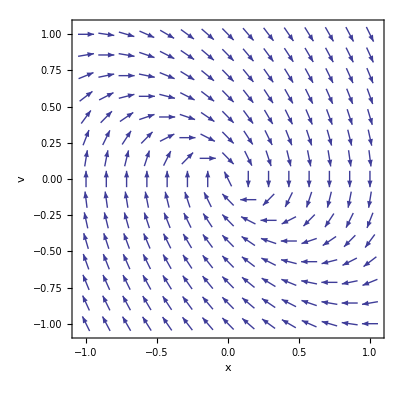

```mathematica
f[x_,v_] = -x - v;
VectorPlot[{v,f[x,v]},{x,-1,1},{v,-1,1},AspectRatio->Automatic, VectorScale->{0.04,.8,None},FrameLabel->{"x","v"}]
```

## Conservation of Phase-Space Area

The solutions of the damped oscillator ODE do not conserve phase-space area. By this we mean the following: consider an area of phase-space, say a square, whose boundary is mapped out by a collection of initial conditions. As these points evolve in time according to the ODE, the square changes shape. The area of the square shrinks as all points are attracted toward the origin. (See Fig. 1.5.)

Fig. 1.5 Flow of a set of initial conditions for f(x,v) = -x - v.

Dissipative systems -- systems that lose energy-- have the property that phase-space area shrinks over time. On the other hand, nondissipative systems , which conserve energy, can be shown to conserve phase-space area. Consider, for example, the direction field associated with motion in a potential V(x). Newton's equation of motion is m (ⅆ^2 x)/(ⅆ t^2)=-(∂V)/(∂x), or in terms of phase-space coordinates (x,v),

ⅆx/ⅆt=v,
ⅆv/ⅆt=-1/m(∂V)/(∂x).

According to Eq. (1.2.10), the projection of the direction field onto the (x,v) plane has components (v, -1/m(∂V)/(∂x) ). One can prove that this flow is area-conserving by showing that it is divergence-free. It is easiest at first to discuss such flows in the (x,y) plane, rather than the (x,v) plane. A flow in the (x,y) plane, described by a vector field v(x,y)=(v_x(x,y),v_y(x,y)), is divergence-free if the flow satisfies

∇·v(x,y)=(∂v_x)/(∂x)|_y+(∂v_y)/(∂y)|_x= 0,

where we have explicitly shown what is held fixed in the derivatives.  The connection between this divergence and the area of the flow can be understood by examining  Fig. 1.6, which depicts an area S moving with the flow. The  differential change ⅆS in the area as the boundary C moves by  ⅆr is ⅆS=∮_C ⅆr·n̂ⅆl,  where ⅆl is a line element along C, and n̂ is the unit vector normal to the edge, pointing out from the surface. Dividing by ⅆt, using v=ⅆr/ⅆt, and applying the divergence theorem,  we obtain

ⅆS/ⅆt=∮_C v·n̂ⅆl=∫_S ∇·vⅆ^2 r.

Thus, the rate of change of the area ⅆS/ⅆt equals zero if ∇·v=0, proving that divergence-free flows are area-conserving.

Fig. 1.6  Surface  S moving by ⅆrin time ⅆt.

Returning to the flow of the direction field in the (x,v) plane given by Eq. (1.2.11),  the x-component of the flow field is v,  and the v-component is -1/m(∂V)/(∂x) . The divergence of this flow is, by analogy to Eqs. (1.2.12),

(∂v)/(∂x)|_v+∂/(∂v)(-1/m(∂V)/(∂x))|_x=0.

Therefore, the flow conserves phase  space area. Mathematicans refer to such flows as symplectic flows.

Why should we care whether a flow is area-conserving?  Because the direction field for area-conserving flows looks very different than that for a non-area-conserving flow such as the damped harmonic oscillator. In area-conserving flows, there are no attracting fixed points toward which orbits fall; rather, the orbits tend to circulate indefinitely. This property is epitomized by the phase-space flow for the undamped harmonic oscillator, shown in Fig. 1.7

Fig. 1.7 phase-space flow and constant-H curves for the undamped harmonic oscillator, f(x,v) = -x.

## Hamiltonian Systems

Equations (1.2.11) are a specific example of a more general class of area-conserving flows called Hamiltonian flows. These flows have equations of motion of the form

ⅆx/ⅆt=(∂H(x,p,t))/(∂p),

 ⅆp/ⅆt=-(∂H(x,p,t))/(∂x),

where p is the momentum associated with the variable x The function H(x,p,t) is the Hamiltonian of the system. These flows are area-conserving, because their phase-space divergence is zero:

∂/(∂x)ⅆx/ⅆt+∂/(∂p)ⅆp/ⅆt=(∂^2 H(x,p,t))/(∂x∂p)-(∂^2 H(x,p,t))/(∂x∂p)=0.

For Eqs. (1.2.11), the momentum is p = m v, and the Hamiltonian is the total energy of the system, given by the sum of kinetic and potential energies:

H=(m v^2)/2+V(x)=p^2/(2 m)+ V(x).

If the Hamiltonian is time-independent, it can easily be seen that the direction field is everywhere tangent to surfaces of constant H. Consider the change ⅆH in the value of H as a particle follows along the flow for a time ⅆt. This change is given by

ⅆH=ⅆx (∂H)/(∂x)+ⅆp (∂H)/(∂p)=ⅆt((∂H)/(∂x)ⅆx/ⅆt+(∂H)/(∂p)ⅆp/ⅆt)

Using the equations of motion, we have

ⅆH=ⅆt[(∂H)/(∂x)(∂H)/(∂p)+(∂H)/(∂p)(-(∂H)/(∂x))]=0

In other words energy is conserved, so that the flow is along constant-H surfaces. Some of these constant H surfaces are shown in Fig. 1.7 for the harmonic oscillator. As usual, we plot the direction field in the (x,v) plane rather than in the (x,p) plane.

For a time-independent Hamiltonian H(x,p), curves of constant-H  are nested curves in phase-space,  which describe the orbits.  Even for very complicated Hamiltonian functions, these constant-H curves must be nested (think of contours of constant altitude on a topographic map). The resulting orbits must always remain on a given constant-H contour in a given region of phase-space. Different regions of phase-space are isolated from one another by these curves. Such motion is said to be integrable.

However, this situation can change if the Hamiltonian depends explicitly on time so that energy is not conserved, or if phase-space has four or more dimensions [as, for example,  can occur for two coupled oscillators, which have phase-space (x_1,v_1,x_2,v_2)]. Now energy surfaces no longer necessarily isolate different regions of phase-space. In these situations, it is possible for particles to explore large regions of phase-space. The study of such systems is a burgeoning area of mathematical physics called chaos theory. A comprehensive examination of the properties of chaotic systems would take us too far afield, but we will consider a few basic properties of chaotic systems in Sec. 1.4.

Exercises for Sec. 1.2

(1) Find, by hand,  three valid solutions to ((ⅆ^2 x)/(ⅆ t^2))^3=t x(t), x(0)=x'(0)=0. (Hint: Try solutions of the form a t^nfor some constants a and n.)

(2) Plot the direction field for the following differential equations in the given ranges, and discuss the qualitative behavior of solutions for initial conditions in the given ranges of y:

(a)	ⅆy/ⅆt=√t y^2, 0<t< 4,  -2<y<2.

(b)	ⅆy/ⅆt=sin(t+y) ,0<t<15,-8<y<8 .

(Hint: You can increase the resolution of the vector field using the VectorPoints option, as in VectorPoints→25.)

(3) For a Hamiltonian H(x,v,t), that depends explicitly on time, show that rate of change of energy ⅆH/ⅆt along a particular trajectory in phase-space is given by

ⅆH/ⅆt=(∂H)/(∂t)|_(x,v)

(4) A simple pendulum follows the differential equation θ''(t)=-g/lsin θ(t), where θ is the angle the pendulum makes with the vertical, g=9.8 m/s^2 is the acceleration of gravity, and l is the length of the pendulum. (See Fig. 1.8).

Fig. 1.8 Simple pendulum

Plot the direction field for this equation projected into the phase-space (θ,θ'), in the ranges -π < θ < π and -4 s^-1 < θ'  < 4 s^-1 , assuming a length l of 10 m.

(a) Discuss the qualitative features of the solutions. Do all phase-space trajectories circle the origin? If not, why not? What do these trajectories correspond to physically?

(b) Find the energy H for this motion in terms of θ and θ'. Plot several curves of constant H on top of your direction field, to verify that the field is tangent to them.

(5) Find an expression for the momentum p_θ associated with the variable θ, so that  one can write the equations of motion for the pendulum in Hamiltonian form,

ⅆθ/ⅆt=(∂H(θ,p_θ,t))/(∂p_θ),
(ⅆ p_θ)/ⅆt=-(∂H(θ,p_θ,t))/(∂θ).		 .

(6) The Van der Pol oscillator ODE models some properties of excitable systems, such as heart muscle or certain electronic circuits. The ODE is

x''+(x^2-1)x'+x=0.

The restoring force is a simple Hooke's law, but the "drag force" is more complicated, actually accelerating "particles" with |x|<1.  (Here, x could actually mean the oscillation amplitude of a chunk of muscle, or the current in a nonlinear electrical circuit.) At low amplitudes the oscillations build up, but at large amplitudes they decay.

(a) Draw the direction field projected into the phase-space (x,x') for -2<x<2, -2<x'<2.  Discuss the qualitative behavior of solutions that begin (i) near the origin, (ii) far from the origin.

(b) Does this system conserve phase-space area, where (x,x') is the phase-space?

(7) A particle orbiting around a stationary mass M (the sun, for example) follows the following differential equation for radius as a function of time, r(t) where r is the distance measured from the stationary mass:

(ⅆ^2 r)/(ⅆ t^2)=L^2/r^3-(G M)/r^2.

Here,  G is the gravitational constant, and  L  is a constant of the motion - the specific angular momentum of the particle, determined by radius r and angular velocity  θ̇  as

L=r^2 θ̇.

(a) Assuming that L is nonzero, find a transformation of time and spatial scales, r̄=r/a,t̄=t/t_o, that puts this equation into the dimensionless form

(ⅆ^2_
r)/(ⅆ(t̄)^2)=1/(_
r)^3-1/(_
r)^2.

(b) Plot the projection of the direction field for this equation into the phase-space  (r̄,r̄') in the range 0.1< r̄<4, -0.7<r̄'<0.7.

(i) What is the physical significance of the point (r̄,r̄')=(1,0)?

(ii) What happens to particles that start with large radial velocities at large radii, r̄>>1?

(iii) What happens to particles with zero radial velocities at small radius, r̄<<1?  Explain this in physical terms.

(iv) For particles that start with velocities close to the point  (r̄,r̄')=(1,0), the closed trajectories correspond to elliptical orbits, with the two points where  r̄'=0 corresponding to distance of closest approach r_o(perihelion) and farthest distance (r̄)_1 (aphelion) from the fixed mass. Therefore, one closed orbit in the (r̄,r̄') plane corresponds to a whole set of actual orbits with different scale parameters a and t_o but the same elliptical shape. How do the periods of this set of orbits scale with the size of the orbit? (This scaling is sometimes referred to as Kepler's third law.)

(c) Find the Hamiltonian H(r̄,r̄') associated with the motion described above. Plot a few curves of constant H on top of the direction field, verifying that the field is everywhere tangent to the flow.

(8) Magnetic and electric fields are often visualized by drawing the field lines associated with these fields. These field lines are the trajectories through space that are everywhere tangent to the given field. Thus, they are analogous to the trajectories followed by particles as they propagate tangent to the direction field. Consider a field line that passes through the point r=r_o. We parametrize this field line by the displacement s measured along the field line from the point r_o. Thus, the field line is given by a curve through space, r=r(s), where r(0)=r_o.

A displacement ⅆr along the field line with magnitude ⅆs is in the direction of the local field: ⅆr=ⅆs E(r)/|E(r)|. Dividing by ⅆs yields the following differential equation for the field line:

ⅆ/ⅆs r(s)=E(r)/|E(r)|.

Equation (1.2.24) is a set of coupled first-order ODEs for the components of r(s), with initial condition r(0)=r_o.

(a) Using VectorPlot plot the electric field E(x,y)=-∇ϕ(x,y) that arises from the following electrostatic potential ϕ(x,y):

ϕ(x,y) = x^2-y^2.

(This field satisfies Laplace's equation, ∇^2 ϕ=0 .) Make the plot in the ranges  -2<x<2, -2<y<2  .

(b) Show that for this potential, Eq. (1.2.24) implies that ⅆy/ⅆx = -y/x along a field line. Solve this ODE analytically to obtain the general solution for  y(x), and plot the resulting field lines in the (x,y) plane for initial conditions (x_o,y_o) = (m, n) where m=-1,0,1 and n=-1,0,1 (nine plots in all). Then superimpose these plots on the previous plot of the field. [Hint 1: Make a table of plots, then use a single Show command to superimpose them.] Hint 2: (ⅆx/ⅆs) / (ⅆy/ⅆs) = ⅆx/ⅆy.]

## 1.3 Analytic Solution of Initial-Value Problems via DSolve

1.3.1 DSolve

The solution to some  (but not all) ODEs can be determined analytically. This section will discuss how to use Mathematica's analytic differential equation solver DSolve in order to find these analytic solutions.

Consider a simple differential equation with an analytic solution, such as the harmonic oscillator equation

(ⅆ^2 x)/(ⅆ t^2)=-ω_o^2x.

DSolve can provide the general solution to this second-order ODE . The syntax is as follows:

DSolve[ODE, unknown function, independent variable].

The ODE is written as a logical expression, x''[t]==-ω_o^2x[t] . Note that in the ODE you must refer to x[t] , not merely x as we did in Eq. (1.3.1). The unknown function is x(t) in this example. Then we specify the independent variable t, and evaluate the cell:

```mathematica
DSolve[x''[t]==-Subscript[ω, o]^2 x[t],x[t],t]
```

{{x[t]→C[2] Cos[t ω_o]+C[1] Sin[t ω_o]}}

The result is a list of solutions (in this case there is only one solution), written in terms of two undetermined constants, C[1] and C[2]. As we know, these constants  are set by specifying initial conditions.

It is possible to obtain a unique solution to the ODE by specifying particular initial conditions in DSolve. Now the syntax is

DSolve[{ODE, initial conditions},unknown function, independent variable].

Just as with the ODE, the initial conditions are specified by logical expressions, not assignments, for example,   x[0]==x0, v[0]== v0:

```mathematica
DSolve[{x''[t]==-Subscript[ω, o]^2 x[t],
              x[0]==x0,x'[0]==v0},x[t],t]
```

{{x[t]→x0 Cos[t ω_o]+(v0 Sin[t ω_o])/ω_o}}

As expected, the result matches our previous solution, Eq. (1.1.9).

DSolve can also be used to provide solutions to systems of coupled ODEs. Now, one provides a list of ODEs in the first argument, along with a list of the unknown functions in the second argument. For instance, consider the following coupled ODEs, which describe a set of two coupled harmonic oscillators with positions x1[t] and x2[t], and with given initial conditions:

```mathematica
DSolve[{x1''[t]==-x1[t] + 2(x2[t]-x1[t]),  
              x2''[t]==-x2[t] + 2 (x1[t]-x2[t]),x1[0]==0,x1'[0]==0,x2[0]==1,x2'[0]==0},{x1[t],x2[t]},t]
```

{{x1[t]→-1/4 ⅇ^(-ⅈ t-ⅈ √5 t) (ⅇ^(ⅈ t)-ⅇ^(ⅈ √5 t)-ⅇ^(2 ⅈ t+ⅈ √5 t)+ⅇ^(ⅈ t+2 ⅈ √5 t)),x2[t]→1/4 ⅇ^(-ⅈ t-ⅈ √5 t) (ⅇ^(ⅈ t)+ⅇ^(ⅈ √5 t)+ⅇ^(2 ⅈ t+ⅈ √5 t)+ⅇ^(ⅈ t+2 ⅈ √5 t))}}

Mathematica found the solution, although it is not in the simplest possible form. For example, x1[t] can be simplified by applying FullSimplify:

```mathematica
FullSimplify[x1[t]/.%[[1]]]
```

1/2 (Cos[t]-Cos[√5 t])

Mathematica  knows how to solve a large number of quite complex ODEs analytically. For example, it can find the solution to a harmonic oscillator ODE where the square of the natural frequency ω_o is time-dependent, decreasing linearly with time : ω_o^2=- t .  This ODE is called the Airy equation:

x''(t)=t x(t).

The general solution to this equation is

```mathematica
DSolve[x''[t] - t x[t]==0,x[t],t]
```

{{x[t]→AiryAi[t] C[1]+AiryBi[t] C[2]}}

The two independent solutions to the ODE are special functions called Airy  functions, Ai(x) and Bi(x). These are called special functions in order to distinguish them from the elementary functions  such as sin x or log x that appear on your calculator. Mathematica  refers to these functions as AiryAi[x] and AiryBi[x]. These are only two of the huge number of special functions that Mathematica knows. Just as for the elementary functions, one can plot these special functions, as shown in Cell 1.12.

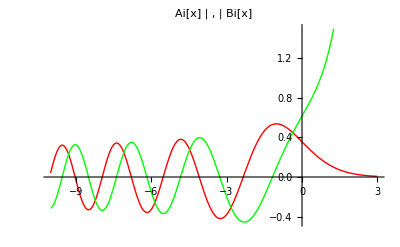

```mathematica
Plot[{AiryAi[x],AiryBi[x]},{x,-10,3},PlotStyle->{Red,Green},PlotLabel->Grid[{{Style["Ai[x]",FontColor->Red],",",Style["Bi[x]",FontColor->Green]}},Spacings->.2]]
```

On the other hand, there are many seemingly straightforward ODEs that have no solution in terms of either special functions or elementary functions. Here is an example:

```mathematica
DSolve[x'[t] ==t/(x[t]+t)^2,x[t],t]
```

DSolve[x'[t]==t/(t+x[t])^2,x[t],t]

Mathematica could not find an analytic solution for this simple first-order ODE, although if we wished we could plot the direction field to find the qualitative form of the solutions. Of course, that doesn't mean that there is no analytic solution in terms of predefined functions - after all, Mathematica is not omniscient. However, as far as I know there really is no such solution to this equation.

You may wonder why a reasonably simple first-order ODE has no analytic solution, but a second-order ODE like the Airy equation does have an analytic solution. The reason in this instance is mainly historical, not mathematical. The solutions of the Airy equation are of physical interest, and were explored originally by the British mathematician George B. Airy. The equation is important in the study of wave propagation through inhomogeneous media, and in the quantum theory of tunneling, as we will see in Chapter 5.  Many of the special functions that we will encounter in this course - Bessel functions, Mathieu functions, Legendre functions, etc. - have a similar history: they were originally studied because of their importance to some area of science or mathematics.

Our simple first-order ODE, above, has no analytic solution (as far as I know) simply because no one has ever felt the need to define one.  Perhaps some day the need will arise, and the solutions will then be detailed and named.

However, there are many ODEs for which no exact analytic solution can be written down.  These ODEs have chaotic solutions that are so complex that they cannot be predicted on the basis of analytic formulae. Over long times, the solutions cannot even be predicted numerically with any accuracy (as we will see in the next section).
	The syntax for DSolve is summarized in Table 1.1.

Table 1.1  DSolve 
DSolve[eqn,x[t],t] | Solve a differential equation for x[t]
DSolve[{eqn1,eqn2,…},{x1[t],x2[t],…},t] | Solve coupled differential equations

Exercises for Sec. 1.3

(1) In the process of radioactive decay, an atom spontaneously changes form by emitting particles from the nucleus. The rate ν at which this decay happens is defined as the fraction of nuclei that decay per unit of time in a sample of material. Write down and solve a differential equation for the mass of radioactive material remaining at time t, m(t), given an amount m_o at t=0. How long does it take for half the material to decay?

(2) A spaceship undergoing constant acceleration g=9.8 m/s^2 (as felt by the passengers) will follow Newton's second law, with the addition (by Einstein) that the apparent mass of the ship as seen by a stationary  observer will increase with velocity v(t) in proportion to the factor 1/√(1-v^2/c^2). This implies that the velocity satisfies the following first-order ODE:

ⅆ/ⅆt(v/(√(1-v^2/c^2)))=g.

(a)Find the general solution, using pencil and paper, for the position x(t) of the ship (where x(t) and v(t) are related in the usual way, by  v=ⅆ x/ⅆt).

(b) After 100 earth years of acceleration, starting from rest, how far has the ship gone in light-years (one light-year = 9.45 × 10^15m)?

(c) Thanks to relativistic time dilation, the amount of time τ  that has passed onboard the ship is considerably shorter than 100 years, and is given by the solution to the differential equation ⅆτ/ⅆt=√(1-(v(t))^2/c^2),τ(0)=0 . Solve this ODE, using DSolve and the solution for v(t) from part (b) above, to find the amount of time that has gone by for passengers on the ship. (Note: The nearest star is “only” about 4.3 light years from earth).  What was the average speed of the ship over the course of the trip, in units of c, as far as the passengers are concerned?

(3) The charge Q(t) on the capacitor in an L R C electrical circuit obeys a second-order differential equation,

L Q''+R Q'+Q/C=V(t).

(a) Find the general solution to the equation, taking V(t) = 0.

(b)  Plot this solution for the case Q(0) = 10^-5  coulomb, Q'(0)=0, taking R= 10 ohms, C = 10^-5 farad, L =  0.1 henry. What is the frequency of the oscillation being plotted (in radians per second)? What is the rate of decay of the envelope (in inverse seconds)?

(4) A man throws a pebble straight up. Its height y(t) satisfies the differential equation y''+γ y'=-g, where g is the acceleration of gravity and γ  is the damping rate due to frictional drag with the air.

(a) Find the general solution to this ODE

(b) Find the solution y(t) for the case where the initial speed is 6 m/s, y(0) = 0, and  γ= 0.2 s^-1 . Plot this solution vs. time.

(c) Find the time when the pebble returns to the ground (this may require a numerical solution of an algebraic equation).

(5) Atomic Hydrogen (H) recombines into molecular Hydrogen (H_2) according to the simple chemical reaction H+H⇄H_2. The rate of the forward recombination reaction (number of reactions per unit time per unit volume) is ν_1 n_H^2 , where n_H is the number density (in atoms per cubic meter) of atomic hydrogen, and ν_1 is a constant. The rate of the reverse reaction (spontaneous decomposition into atomic hydrogen) is   ν_2 n_H_2,  where  n_H_2 is the number density of molecular hydrogen.

(a) Write down two coupled first-order ODEs for the densities of molecular and atomic hydrogen as a function of time.

(b) Solve these equations for general initial densities.

(c) Show that the solutions to these equations satisfy n_H+ 2 n_H_2=const.  Take the constant equal to n_o (the total number density of hydrogen atoms in the system, counting those that are combined into molecules), and find the ratio of densities in equilibrium.

(d) Plot the densities as a function of time for the initial condition n_H_2 =1, n_H = 0, ν_1 = 3, and ν_2 = 1.

(6) A charged particle, of mass m  and charge q,  moves in uniform magnetic and electric fields B = (0,0,B_o), E=(E_⊥,0,E_z).  The particle satisfies the nonrelativistic equations of motion,

m ⅆv/ⅆt = q(E + v ×B) .

(a) Find, using DSolve,  the general solution of these coupled first-order ODES for the velocity v(t)=(v_x(t),v_y(t),v_z(t)) .

(b) Note that in general there is a constant velocity perpendicular to B, on which there is superimposed a circular motion. The constant velocity is called an E×B drift. The circular motion is called a cyclotron orbit.  What is the frequency of the cyclotron orbit? What are the magnitude and direction of the E×B drift?

(c) Find v(t) for the case for an electron with r(0)=v(0)=0, E_z = 0, E_⊥ =5000V/m, and B_o = 0.005 tesla (these are the proper S.I. units for the equation of motion as written above). Plot v_x(t) and v_y(t) vs. t for a time of 10^-7 s.

(d) Use the results of part (b) to obtain x(t) and y(t). Plot x vs. y using a parametric plot to look at the trajectory of the electron.  Plot the trajectory again in a frame moving at the E×B drift speed. The radius of the circle is called the cyclotron radius. What is the magnitude of the radius (in meters) for this example?

(7) The trajectory r(θ) of a particle orbiting a fixed mass M  at the origin of the (r,θ) plane satisfies the following differential equation:

L/r^2 ⅆ/ⅆθ(L/r^2 ⅆr/ⅆθ)-L^2/r^3=-(G M)/r^2,

where L is the specific angular momentum, as in Eq. (1.2.22).

(a) Introduce a scaled radius  r̄=r/a to show that with proper choice of a this equation can be written in dimensionless form as

1/(_
r)^2 ⅆ/ⅆθ(1/(_
r)^2(ⅆ_
r)/ⅆθ)-1/(_
r)^3=-1/(_
r)^2.

(b) Find the general solution for the trajectory, and show that Mathematica's expression is equivalent to the expression  
1/(r(θ))=(G M)/L^2 (e cos(θ-θ_o)+1), where e is the eccentricity and θ_o is the angular position of perihelion. [See Eq. (1.2.21) and Exercise (3) of Sec. 9.6).

(8) Consider the electric field from a unit point dipole at the origin. This field is given by E=-∇ϕ(ρ,z) in cylindrical coordinates (ρ,θ,z), where ϕ=z/(ρ^2+z^2)^(3/2). In cylindrical coordinates the field lines equation, Eq. (1.2.24),  has components

ⅆρ/ⅆs= E_ρ(r)/|E(r)|,
ρ ⅆ θ/ⅆs= E_θ(r)/|E(r)|,
ⅆz/ⅆs= E_z(r)/|E(r)|..

(a) Use DSolve to determine  the field lines for the dipole that pass through the following points:
(ρ_o,z_o)=(1, 0.5 n), where n=1,2,3,4 . Make a table of plots of these field lines in the (ρ,z) plane and superimpose them all with a Show command to visualize the field lines from this dipole. 
(Hint: Show that ⅆz/ⅆρ= E_z/E_ρ and solve this ODE for z(ρ) using DSolve. Plot the resulting curves in the (ρ,z) plane for the given initial conditions: z(1) = 0.5 n.)

(b) A simple analytic form for the field lines from a dipole.can be found in spherical coordinates (r,θ,ϕ). In these coordinates r(s)=(r(s),θ(s),ϕ(s)) and Eq. (1.2.24) becomes

ⅆr/ⅆs= E_r(r)/|E(r)|,
r ⅆ θ/ⅆs= E_θ(r)/|E(r)|,
r sinθⅆϕ/ⅆs= E_ϕ(r)/|E(r)|.

Also, since r=√(ρ^2+z^2) and z=r cosθ, the dipole potential has the form ϕ(r,θ)=cosθ/r^2. An equation for the variation of r with θ along a field line can be obtained  as follows:

1/r ⅆr/ⅆθ=(ⅆr/ⅆs)/(r ⅆ θ/ⅆs)=(E_r(r,θ))/(E_θ(r,θ)) .

Solve this differential equation for r(θ) with initial condition r(θ_o)=r_o to show that the equation for the field lines of a point dipole  in spherical coordinates is

r(θ)=r_o sin^2 θ/sin^2 θ_o.

Superimpose plots of r(θ) for r_o=1,2,3,4 and θ_o=π/2.

## 1.4 Numerical Solution of Initial-Value Problems

1.4.1 NDSolve

Mathematica  can solve ODE initial-value problems numerically via the intrinsic function NDSolve . The syntax for NDSolve is almost identical to that for DSolve:

NDSolve[{ODE, initial conditions},x[t],{t,tmin,tmax}]

Three things must be remembered when using NDSolve:

(1) Initial conditions must always be specified.

(2) No non-numerical constants can appear in the list of ODEs or the initial conditions.

(3) A finite interval of time must be provided, over which the solution for x(t) is to be determined.

As an example,  we will solve the problem from the previous section that had no analytic solution, for the specific initial condition x(0) = 1:

```mathematica
NDSolve[{x'[t] ==t/(x[t] + t)^2,x[0]==1},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

The result is a list of possible substitutions for x(t), just as when using DSolve. However, the function x(t) is now determined numerically via an InterpolatingFunction. These InterpolatingFunctions are also used for interpolating lists of data (see Sec. 9.11). The reason why an InterpolatingFunction is used by NDSolve will become clear in the next section, but can be briefly stated as follows: When NDSolve numerically solves an ODE, it finds  values for x(t) only at specific values of t between tmin and tmax, and then uses an InterpolatingFunction to interpolate between these values of t.

As discussed in Sec. 9.11 , the InterpolatingFunction can be evaluated at any point in its range of validity from tmin to tmax.  For example, we can plot the solution by first extracting the function from the list of possible solutions,

```mathematica
x[t]/.%[[1]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

and then plotting the result, as shown in Cell 1.16.

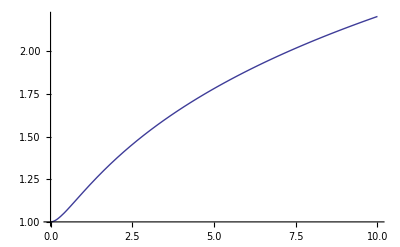

```mathematica
Plot[%,{t,0,10}]
```

Now we come to an important question: how do we know that the answer provided by NDSolve is correct? The numerical solution clearly matches the initial condition, x(0) = 1.  How do we tell if it also solves the ODE? One way to tell this is to plug the solution back into the ODE to see if the ODE is satisfied. We can do this just as we have done with previous analytic solutions, except that the answer will now evaluate to a numerical function of time, which must then be plotted to see how much it differs from zero (see Cell 1.17).

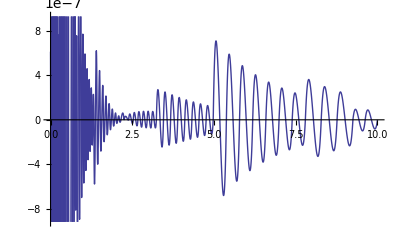

```mathematica
x[t_] = %%;
error[t_] = x'[t] - t/(x[t]+t)^2;
Plot[error[t],{t,0,10}]
```

The plot shows that the error in the solution is small, but nonzero.

In order to further investigate the accuracy of NDSolve,  we will solve a problem with an analytic solution: the harmonic oscillator with frequency ω_o  = 1, and with initial condition x(0)= 1, x'(0) = 0. The exact solution is x(t) = cos t.  NDSolve provides a numerical solution that can be compared with the exact solution, as shown in Cell 1.20.

```mathematica
Clear[x];
NDSolve[{x''[t] == -x[t],x[0]==1,x'[0]==0},x[t],{t,0,30}]
```

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

```mathematica
x[t]/.%[[1]]
```

InterpolatingFunction[{{0.,30.}},<>][t]

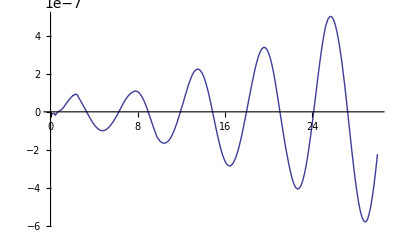

```mathematica
Plot[% - Cos[t],{t,0,30}]
```

The difference between NDSolve's solution and cos t is finite, and is growing with time. This is typical behavior for numerical solutions of initial-value problems: the errors tend to accumulate over time.  If this level of error is too large,  the error can be reduced by using some combination of the following options for NDSolve: WorkingPrecision, AccuracyGoal, PrecisionGoal, and InterpolationOrder. The default for WorkingPrecision is $MachinePrecision, just as for FindRoot. The default value of AccuracyGoaland PrecisionGoal is usually set at WorkingPrecision/2.  We can intercede, however, choosing our own number of significant figures for the accuracy.  It is usually easiest to set both AccuracyGoal and PrecisionGoal to about the same number, and of course this number should be smaller than WorkingPrecision (otherwise the requested accuracy cannot be achieved due to numerical roundoff error). Good values for my computer (with $MachinePrecision of 16) are AccuracyGoal→13, PrecisionGoal→13:

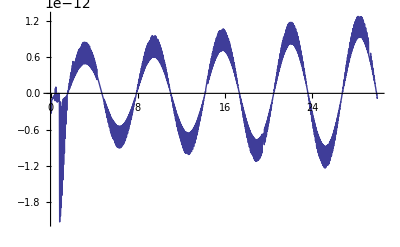

```mathematica
xsol[t_] = x[t]/.NDSolve[{x''[t] == -x[t],x[0]==1,x'[0]==0},x[t],{t,0,30},AccuracyGoal->13,PrecisionGoal->13][[1]];
Plot[xsol[t] - Cos[t],{t,0,30}]
```

The error in the solution has now been considerably reduced.  If even higher accuracy is required, we can set WorkingPrecision to a larger value than $MachinePrecision. However, be warned that this only increases the precision of the solution at the evaluated points, not at interpolated values between these points. Since a finite number of points must necessarily be used in obtaining the interpolated solution, the error in the solution will generally be much larger between the points than at them. One can reduce this interpolation error by increasing the order of the interpolation used, setting InterpolationOrder->5, for instance. An example is shown in Cell 1.22.

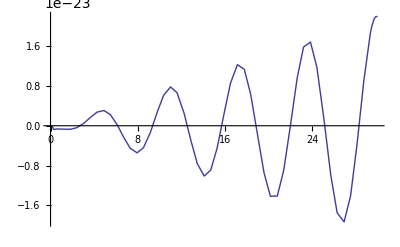

```mathematica
xsol[t_] = x[t]/.NDSolve[{x''[t] == -x[t],x[0]==1,x'[0]==0},x[t],{t,0,30},WorkingPrecision->50,InterpolationOrder->5][[1]];
Plot[xsol[t] - Cos[t],{t,0,30},WorkingPrecision->50]
```

The numerical error is in this example has been reduced to a few parts in 10^23.  Note that WorkingPrecision must  also be increased in the plot in order to  evaluate the error with sufficient accuracy. The reader is invited to vary the values of the options in NDSolve to test the behavior of the error.

1.4.2 Error in Chaotic Systems

## A Chaotic System: The Driven Pendulum

The problem of error accumulation in numerical solutions of ODEs is radically worse when the solutions display chaotic behavior.  Consider the following equation of motion for a pendulum of length l (see Fig. 1.8):

l θ''(t) = -g sin θ-f sin(θ-ω t).

The first term on the right-hand side is the usual acceleration due to gravity, and the second term is an added time-dependent  force that can drive the pendulum into chaotic motion.  This term can arise if one rotates the pivot of the pendulum in a small circle, at frequency ω. (Think of a noisemaker on New Year's Eve.)

We can numerically integrate this equation of motion using NDSolve.  In Fig. 1.9 we show θ(t)  for 0<t<200, taking l=g =f= 1  and  ω = 2,  and initial conditions θ(0) = -0.5, θ'(0) = 0.

Fig. 1.9 Two trajectories starting from the same initial conditions. The upper trajectory is integrated with higher accuracy than the lower trajectory.

The commands in Cell 1.23 integrate the equation of motion along the lower trajectory plotted in Fig 1.9 , and plot the motion of the pendulum as an animation. For later purposes we solve the ODE as two coupled first-order ODEs for θ(t) and v(t), where v=θ' is the angular velocity.

```mathematica
z = {θ[t],v[t]}/.NDSolve[{θ'[t] == v[t],v'[t] == -Sin[θ[t]] - Sin[θ[t] - 2 t],θ[0] ==-0.5,v[0] ==0},{θ[t],v[t]},{t,0,200}][[1]];
Table[ListPlot[{{0,0},{Sin[z[[1]]],-Cos[z[[1]]]}},Joined->True,Epilog->{PointSize[0.018],Point[{Sin[z[[1]]],-Cos[z[[1]]]}]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{t,0,30,.2}];
ListAnimate[%]
```

One can see in Fig. 1.9 that θ(t) increases with time in a rather complicated manner as the pendulum rotates about the pivot, and sometimes  doesn’t quite make it over the top. (Values of θ larger than 2 π mean that the pendulum has undergone one or more rotations about the pivot, as shown in the animation.)

If we now repeat this trajectory , but increase the accuracy by setting AccuracyGoal->13 and PrecisionGoal->13, the results for the new trajectory at late times ( the upper curve in Fig. 1.9) bears little or no resemblance to the lower-accuracy solution. This is because at some point in time one trajectory makes it over the top, but the other does not, and so the two trajectories diverge.

The difference Δθ between the two θ(t) results is shown in Fig. 1.10. The error is exploding with time, as opposed to the relatively gentle increase observed in our previous examples.  The explosive growth of accumulated error is a general feature of chaotic systems. In fact, one can show that if one compares a given trajectory with groups of nearby trajectories , on average the difference between these trajectories increases exponentially  with time: |Δθ|~ exp(λt). The rate of exponentiation of error, λ,  is called the Lyapunov exponent.

Fig. 1.10 Difference between the trajectories of Fig. 1.9.

This rapid error accumulation is the signature of a chaotic system. It makes it impossible to determine trajectories accurately over times long compared to 1/λ.  One can easily see why this is so: a fast computer working at double-double precision (32-digit accuracy) can integrate for times up to roughly ln(10^32)/λ~ 70/λ before roundoff error in the 32nd digit causes order-unity deviation from the exact trajectory. To integrate accurately up to t=7000/ λ, the accuracy would have to be increased by a factor of ⅇ^100 = 2.6 × 10^43 !  Such a high accuracy might somehow be achieved, but evenutally, for sufficiently long integration times t, even the most powerful computer systems will fail to provide accurate results for the trajectory.

For chaotic systems,  small errors in computing  the trajectory, or in the initial conditions, lead to exponentially large errors at later times, making the trajectory effectively unpredictable.

Chaotic trajectories are not an isolated feature of only a few unusual dynamical systems. Rather, chaos is the norm. It has been shown that almost all dynamical systems are chaotic. Integrable systems such as the harmonic oscillator are the truly unusual cases, even though such cases are emphasized in elementary books on mechanics (because they are analytically tractable).

Since almost all systems are chaotic, and since chaotic systems are unpredictable, one might question the usefulness of Newton's formulation of dynamics, wherein a given initial condition, together with the force law, is supposed to provide all the information necessary to predict future behavior. For chaotic systems this predictive power is lost.

Fortunately, even chaotic systems have features that can be predicted and reproducibly observed. Although specific particle trajectories cannot be predicted over long times, average values based on many particle trajectories are reproducible. We will examine this statistical approach to complex dynamical systems in Chapter 8.

## The Lyapunov Exponent

One example of a reproducible average quantity for a chaotic system is the Lyapunov exponent itself.  In order to define the Lyapunov exponent, note that since error accumulates on average as exp(λt), the logarithm of the error should increase linearly with t, with a slope equal to λ.

Therefore, λ  is defined as follows: Consider a given initial condition z_o=(θ_o,v_o).  For this choice, the phase-space trajectory is z(t, z_o)=(θ(t,θ_o,v_o),v(t,θ_o,v_o)). Now consider a small displacement d_o = (Δθ_o,Δv_o) to a nearby initial condition, z_o + d_o.

The Lyapunov exponent is defined as

λ(z_o)= lim_(t→ ∞,|d_o|→ 0) ⟨1/t ln ((|z(t,z_o+d_o)-z(t,z_o)|)/(|d_o|))⟩

where the ⟨ ⟩ stands for an average over many infinitesimal initial displacements d_o in different directions, and | z | corresponds to a vector magnitude in the phase-space. [Units are unimportant in this vector magnitude: both position and momentum can be regarded as dimensionless, so that z can be thought of  as a dimensionless vector for the purposes of Eq. (1.4.2).]

We can numerically evaluate the Lyapunov exponent by averaging over a number of orbits nearby to a given initial condition, all with small  |d_o|.  Then by plotting the right-hand side of Eq. (1.4.2) as a function of time for 0<t<50, we can observe that this function asymptotes to a constant value, equal to λ.

We will do this for our previous example of pendulum motion using the following Mathematica statements.

First, we use the previous phase-space trajectory z(t,z_o) with the initial conditions, θ(0)=-0.5 ,v(0)=0, evaluated in Cell 1.23.

This trajectory is the same as the lower trajectory shown in Fig. 1.9. Next,  we create 40 nearby initial conditions by choosing values of θ(0) and v(0) scattered randomly around the point (-0.5,0):

```mathematica
z0 = Table[{-0.5+10^-5(2RandomReal[]-1),10^-5(2RandomReal[]-1)},{40}];
```

Then, we integrate these initial conditions forward in time using NDSolve, and evaluate the vector displacement between the resulting trajectories and the test trajectory z:

```mathematica
Δz[t_] = Table[Norm[{θ[t],v[t]}-z]/.NDSolve[{θ'[t] == v[t],v'[t] == -Sin[θ[t]] - Sin[θ[t] - 2 t],θ[0] ==z0[[m,1]],v[0] ==z0[[m,2]]},{θ[t],v[t]},{t,0,50}][[1]],{m,1,40}];
```

Finally, we evaluate ln[Δz(t)/Δz(0)]/t, averaged over the 40 trajectories, and plot the result in Cell 1.26.

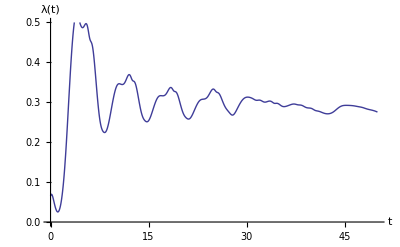

```mathematica
λ[t_] = 1/40 Sum[Log[Δz[t][[n]]/Δz[0][[n]]],{n,1,40}]/t;
Plot[λ[t],{t,0,50},PlotRange->{0,0.5},AxesLabel->{"t","λ(t)"}]
```

The Lyapunov exponent can be seen to asymptote to a fairly constant value of about 0.3 at large times. Fluctuations in the result can be reduced by keeping more trajectories in the average. Thus, over a time t=50, nearby orbits diverge in phase-space  by a factor of ⅇ^(0.3× 50)=3.×10^6, on average. Over a time t=500, initially nearby orbits diverge by the huge factor of 10^65. Even a tiny initial error gets blown up to a massive deviation over this length of time, leading to almost complete loss of predictability.

Note that the choice of d_o in the above numerical work is a rather tricky business. It must be larger than the intrinsic error of the numerical method, otherwise the effect of d_o on the trajectory is swamped by numerical error. But on the other hand, d_o must not be so large that orbits diverge by a large amount over the plotted time interval; otherwise we are not properly evaluating the difference between "infinitesimally nearby trajectories"; that is, we require |d_o| ⅇ^(λ t)<<1.  As a result of these trade-offs, this method for determining λ is not particularly accurate, but it will do for our purposes. More accurate (and complicated!)  methods exist for determining a Lyapunov exponent: see, for example, A.J. Lichtenberg and M. A. Lieberman (1992, p. 315).

1.4.3 Euler's Method

In this section, we will create our own ODE solver by first considering a simple (and crude) numerical method called Euler's method. Most ODE solvers are at their core merely more complex and accurate versions of Euler's method, so we will begin by examining this simplest of numerical ODE solvers. We will then consider more complicated numerical methods.

Euler's method applies to the simple first-order ODE discussed in Sec. 1.2:

ⅆv/ⅆt=f(t,v),  v(0)=v_o.

Later, we will see how to modify Euler's method to apply to more general ODEs.

To apply Euler's method to Eq. (1.4.3), we first discretize the time variable, defining evenly spaced discrete timesteps

t_n=n Δt ,  n=0,1,2,3,....

The quantity Δt is called the step size. (Confusingly, some authors also refer to Δt as the timestep.) We will evaluate the solution v(t) only at the discrete timesteps given in Eq. (1.4.4). Later, we will interpolate to find v(t) at times between the timesteps.

Next, we integrate both sides of Eq. (1.4.3) , and apply the fundamental theorem of calculus:

∫_(t_(n-1))^t_n ⅆv/ⅆt ⅆt = v(t_n)-v(t_(n-1)) =∫_(t_(n-1))^t_n f(t,v(t))ⅆt.

Note that we must take account of the time variation of v(t) in the integral over f on the right-hand side.

So far, no approximation has been made. However, we will now approximate the integral over f, assuming that Δt is so small that f does not vary appreciably over the range of integration:

∫_(t_(n-1))^t_n f(t,v(t))ⅆt≈Δt f(t_(n-1),v(t_(n-1))) + O(Δt^2).

The error in this approximation scales as Δt^2 (see the exercises), and we use the notation O(Δt^2)  to indicate this fact. The same notation is used in power series expansions (Sec. 9.9), and indicates that if Δt is reduced by a factor of 2, the error in Eq. (1.4.6) is reduced by a factor of 4 (for small Δt).

Equation (1.4.6)  is a very crude approximation to the integral, but it has the distinct advantage that, when used in Eq. (1.4.5), the result is a simple recursion relation for v(t_n) :

v(t_n)=v(t_(n-1)) +Δt f(t_(n-1),v(t_(n-1)))+ O(Δt^2)

Equation (1.4.7) is Euler's method. It is called a recursion relation because the value of v at the nth step is determined by quantities from the n-1st step, which were themselves determined in terms of variables at the n-2nd step, and so on back to the initial condition at t=0.  Recursion relations like this are at the heart of most numerical ODE solvers. Their differences lie mainly in the degree of approximation to the integral in Eq. (1.4.6).

To see how Euler's method works, we will write a program that can be used to solve any ODE of the form of Eq. (1.4.3).  In our code, we will employ the following simple notation for the velocity at timestep n: a function v[n], defined for integer arguments. We will employ the same notation for the time t_n defining a function t[n] = n Δt.  Then Euler's method can be written in Mathematica as

```mathematica
t[n_] := n Δt;
v[n_] := v[n-1] + Δt  f[t[n-1], v[n-1]];
v[0] :=   v0
```

The first line defines the time at step n; the second is Eq. (1.4.7) and the third is the initial condition. Note that delayed evaluation is used for all three lines, since we have not yet specified a step size Δt, an initial condition v_o, or the function f. However, even if these quantities are already specified, delayed evaluation must be used in the second line, since it is a recursion relation: v[n] is determined in terms of previous values of v, and can therefore only be evaluated for a given specific integer value of n.

Note that it is somewhat dangerous to write the code in the form given in Cell 1.27, because it is up to us to ask only for nonnegative integer values of n. If, for example, we ask for v[0.5], the second line will evaluate this in terms of v[-0.5], which is then evaluated in terms of v[-1.5], etc., leading to an infinite recursion:

```mathematica
v[0.5]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit will be suppressed during this calculation.

$Aborted

In such errors,  the kernel will often grind away  fruitlessly for many minutes trying to evaluate the recursive tree, and the only way to stop the process is to quit the kernel. We can improve the code by adding conditions to the definition of v[n]  that require n to be a positive integer:

```mathematica
Clear[v]
```

```mathematica
t[n_] := n Δt;
v[n_] := v[n-1] + Δt  f[t[n-1], v[n-1]]/;n>0 && n∈Integers;
v[0] :=   v0
```

Here we have used the statement n∈Integers , which stands for the logical statement "n is an element of the integers", evaluating to a result of either True or False. The symbol ∈  stands for the intrinsic function Element and is available on the BasicInput palette. (Don't confuse ∈ with the Greek letter epsilon, ϵ.) 
	If we now ask for v[0.5], there is no error because we have only defined v[n] for positive integer argument:

```mathematica
v[0.5]
```

v[0.5]

In principle, we could now run this code simply by asking for any value of v[n] for  n∈Integers   and n>0. Mathematica will then evaluate v[n-1]  in terms of v[n-2], and so on until it reaches v[0]=v0.  The code stops here because the definition v[0]=v0  takes precedence over the recursion relation.

However, there are a few pitfalls that should be avoided.  First, it would not be a good idea to begin evaluating the code right now. We have not yet defined the function f, the step size Δt, or the initial condition v_o. Although Mathematica will return perfectly valid results if we ask for, say, v[2], the result will be a complicated algebraic expression without much value. If we ask for v[100], the result will be so long and complicated that we will probably have to abort the evaluation. Numerical methods are really made for solving specific numerical instances  of the ODE in question.

Therefore, let us solve the following specific problem, which we encountered in Sec. 1.2.1:

f(t,v)=t-v,v(0)=0.

The general solution was given in Eq. (1.2.5), and for v(0)=0 is

v(t)=t+ⅇ^-t-1

Before we solve this problem using Euler's method, there is another pitfall that can be avoided by making a small change in the code. As it stands, the code will work, but it will be very slow, particularly if we ask for v[n]with  n>>1. The reason is that every time we ask for v[n], it evaluates the recursion relations all the way back to v[0], even if it has previously evaluated the values of v[n-1], v[n-2], etc.  This wastes time. It is better to make Mathematica remember values of the function v[n] that it has evaluated previously. This can be done as follows:  in the second line of the code, which specifies v[n], write two equal signs:

```mathematica
v[n_] :=( v[n] =v[n-1] + Δt  f[t[n-1], v[n-1]]  )/; n>0 && n∈Integers;
```

The second equal sign causes Mathematica to remember any value of v[n] that is evaluated by adding this value to the definition of v; then, if this value is asked for again, Mathematica uses this result rather than reevaluating the equation.  Note that we have placed parentheses around part of the right-hand side of the equation. These parentheses must be included when the equation has conditions; otherwise the condition statement will not evaluate properly, because it will attach itself only to the second equality, not the first.

The modified Euler code is as follows:

```mathematica
t[n_] := n Δt;
v[n_] :=(v[n] =
             v[n-1] + Δt  f[t[n-1], v[n-1]])/;
           n>0 && n∈Integers;
v[0] :=   v0
```

Let's now evaluate a solution numerically, from 0<t<4.  To do so, first specify the step size, the function f, and the initial condition:

```mathematica
Δt=0.2;
f[t_,v_] = t-v;
v0 = 0;
```

Next, make a list of  data points {t[n],v[n]}, calling this result our numerical solution:

```mathematica
solution = Table[{t[n],v[n]},{n,0,4/Δt}]
```

{{0,0},{0.2,0},{0.4,0.04},{0.6,0.112},{0.8,0.2096},{1.,0.32768},{1.2,0.462144},{1.4,0.609715},{1.6,0.767772},{1.8,0.934218},{2.,1.10737},{2.2,1.2859},{2.4,1.46872},{2.6,1.65498},{2.8,1.84398},{3.,2.03518},{3.2,2.22815},{3.4,2.42252},{3.6,2.61801},{3.8,2.81441},{4.,3.01153}}

Finally, plot these points with a ListPlot, and compare this Euler solution with the analytic solution of Eq. (1.4.9) by overlaying the two solutions in Cell 1.36.

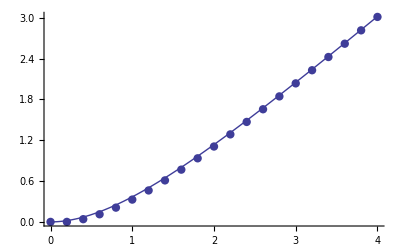

```mathematica
a=ListPlot[solution,PlotStyle->PointSize[0.015]];
b=Plot[E^-t + t -1,{t,0,4}];
Show[a,b]
```

The Euler solution, shown by the dots, is quite close to the exact solution, shown by the solid line.

If we wish to obtain the numerical solution at times between the timesteps we can apply an interpolation to the data and define a numerical function vEuler[t]:

```mathematica
vEuler = Interpolation[solution]
```

InterpolatingFunction[{{0.,4.}},<>]

One thing that we can do with this function is plot the difference between the numerical solution and the exact solution to see the error in the numerical method--see Cell 1.38.

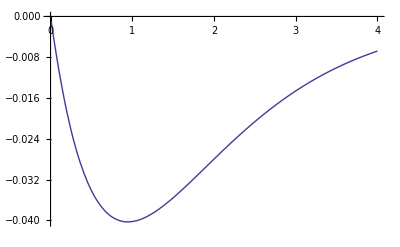

```mathematica
vExact[t_] = E^-t + t - 1;
p1 = Plot[vEuler[t] - vExact[t],{t,0,4}]
```

The error can be reduced by reducing the step size. To do this, we must go back and run the Table command again after setting the step size to a smaller value, and after applying the Clear[v] command.  We must Clear[v] before running the Table command again; otherwise the values of v[1],v[2],… stored in the kernel's memory as a result of our using two equal signs in Eq. (1.4.10),  will supersede the new evaluations.  After clearing v, we must then reevaluate the definition of v in Cell 1.33.

All of these reevaluations are starting to seem like work. There is a way to avoid having to reevaluate several individual cells over and over again. We can create a Module, which is a method of grouping a number of commands together to create a  Mathematica function. Modules are the Mathematica  version of C+ modules or Fortran subroutines, and have the following syntax:

Module[{internal variables}, statements]        creates a module in Mathematica

The list of internal variables defines variables that are used only within the module. The definitions of these variables will not be remembered outside of the module. However, Module creates a set of variables (with names ending with $)  that carry the internal variable values into the Global context once the module has been evaluated. This can sometimes be handy when debugging code. To avoid this, one can instead use the Block command, which has the same syntax as Module but does not create new variables. See the Mathematica documentaion for more information.

Here is a version of the Euler solution  that is written as a module, and assigned to a function Eulersol[v0,time, Δt]. This function finds the approximate solution vEuler[t] for 0<t<time, with step size Δt.  To use the module , all we need to do is specify the function f(t,v) that enters the differential equation:

```mathematica
Eulersol[v0_,time_,Δt_]:= Module[{t,v,solution},
t[n_] := n Δt;
v[n_] :=(v[n] =
             v[n-1] + Δt  f[t[n-1], v[n-1]])/;
           n>0 && n∈Integers;
v[0] :=   v0;
solution = Table[{t[n],v[n]},{n,0,time/Δt}];
vEuler= Interpolation[solution];]
```

Note that we did not have to add a Clear[v] statement to the list of commands, because v is an internal variable that is not remembered outside the module, and is also not remembered from one application of the Module to the next.

Also, note that we don’t really need the condition statements in the definition of v[n] anymore, since we only evaluate v[n]at positive integers, and the definition does not exist outside the Module. 
	In Cell 1.40, we show a plot of the error vs. time as Δt is reduced to 0.1 and then to 0.05. The plot was made simply by running the Eulersol function at these two values of Δt and plotting the resulting error, then superimposing the results along with the original error plot at Δt=0.2.

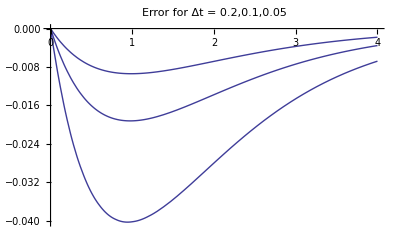

```mathematica
Eulersol[0,4,0.1];
p2 = Plot[vEuler[t]-vExact[t],{t,0,4}];
Eulersol[0,4,0.05];
p3= Plot[vEuler[t]-vExact[t],{t,0,4}];
Show[p1,p2,p3,PlotLabel->"Error for Δt = 0.2,0.1,0.05"]
```

As Δt decreases by factors of 2, the error can be seen to decrease roughly by factors of 2 as well. The error in the solution scales linearly with Δt: Error ∝ Δt. In other words, the error is first-order in Δt .  (The same  language is used in the discussion of power series expansions; see Sec. 9.9.2.)  Euler's method is called a first-order method.

One can see why the error in this method is O(Δt)  from Eq. (1.4.7):  the error in a single step is of order Δt^2. To integrate the solution over a fixed time interval  T,  N steps must be taken, with N=T/Δt increasing as Δt decreases. The total error is the sum of all individual errors, and therefore scales as N Δt^2=T Δt .

Euler's method is too crude to be of much practical use today. Clearly it would be a great improvement in efficiency if we could somehow modify Euler's method so that it is second-order , or even nth-order, with error scaling like Δt^n .  Then by reducing the step size by only a factor of 2, the error would be reduced by a factor of 2^n.  In the next section we will see how to easily modify Euler's method to make it second-order.

The error of a numerical solution to an ODE is controlled by the step size Δt. Reducing the step size increases the accuracy of the solution, but also increases the number of steps required to find the solution over a fixed interval T. For a method with error that is of order n, the error in the solution, found over a fixed time interval T, scales like (Δt)^n.

1.4.4 The Predictor-Corrector Method of Order 2

The error in Euler's method arose from the crude approximation to the integral in Eq. (1.4.6). To improve the approximation, we need a more accurate value for this integral. Now, the required integral is just the area under the function f(v(t),t), shown schematically in Fig. 1.11 (a). Equation (1.4.6) approximates this area by the gray rectangle in Fig. 1.11.a) which is clearly a rather poor approximation to the area under the curve, if the function varies much over the step size Δt.  A better approximation would be to use the average value of the function  at the initial and final points in determining the area:

∫_(t_(n-1))^t_n f(t,v(t))ⅆt≈Δt (f(t_(n-1),v(t_(n-1)))+f(t_n,v(t_n)))/2+O(Δt^3)

Fig. 1.11 different numerical approximations to the area under f
(a) Euler's method Eq. (1.4.6); (b) modified Euler's method,  Eq. (1.4.10).

This approximation would be exactly right if the shaded area above the curve in Fig. 1.11 (b) equaled the unshaded area below the curve.  If f(v(t),t) were a linear function of t over this range, that would be true, and there would be no error. For Δt sufficiently small, f(v(t),t)will be nearly linear in t if it is a smooth function of t, so for small Δt the error is small. In fact, one can easily show that the error in this approximation to the integral is of order Δt^3 (see the exercises at the end of this section), as opposed to the order-Δt^2 error made in a single step of the Euler's method [see Eq. (1.4.6)].  Therefore, this modification to Euler's method should improve the accuracy of the code to order Δt^3in a single step.

If we now use Eq. (1.4.10) in Eq. (1.4.5), we obtain  the following result:

v(t_n)=v(t_(n-1))+Δt (f(t_(n-1),v(t_(n-1)))+f(t_n,v(t_n)))/2+O(Δt^3)

Since the error of the method is order Δt^3in a single step, Eq. (1.4.11) is a distinct improvement over Euler's method, Eq. (1.4.7). However, there is a catch.  Now v(t_n) appears on the right-hand side of the recursion relation, so we can't use this equation as it stands to solve for v(t_n). [We might try to solve this equation for v(t_n), but for general f that is nontrivial. Such methods are called implicit methods, and will be discussed in Chapter 6.]

What we need is some way to replace v(t_n) on the right-hand side: we need a prediction for the value of v(t_n), which we will then use in Eq. (1.4.11) to get a better value. Fortunately, we have such a prediction available: Euler's method, Eq. (1.4.7), provides an approximation to v(t_n), good to order Δt^2. This is sufficient for Eq. (1.4.11), since the O(Δt^2) error in v(t_n) is multiplied in Eq. (1.4.11) by another factor of Δt, making this error O(Δt^3); but  the right-hand side  of Eq. (1.4.11) is already accurate only to O(Δt^3).

The resulting recursion relation is called a predictor-corrector method of order 2.  The method is second-order accurate, because over a fixed time interval T the number of steps taken is T/Δt and the total error scales as (T/Δt) Δt^3=T Δt^2.  The method consists of the following two lines: an initial prediction for v at the nth step, which we assign to a variable v_1 , and the improved correction step, given by Eq. (1.4.11), making use of the prediction:

v_1=v(t_(n-1))+Δt f(t_(n-1),v(t_(n-1))),
v(t_n)=v(t_(n-1))+Δt (f(t_(n-1),v(t_(n-1)))+f(t_n,v_1))/2.

The following module, named PCsol, implements the predictor-corrector method in Mathematica:

```mathematica
PCsol[v0_,time_,Δt_]:=Module[{t,v,f0,v1,solution},t[n_]=n Δt;
v[0]=v0;
f0[n_]:=f[t[n-1],v[n-1]];
v1[n_]:=v[n-1]+Δt f0[n];
v[n_]:=v[n]=v[n-1]+Δt(f0[n]+f[t[n],v1[n]])/2;
solution=Table[{t[n],v[n]},{n,0,time/Δt}];
vPC=Interpolation[solution];]
```

There is one extra trick that we have implemented in this module. We have assigned the value of f at the n-1st step to the variable f0[n], (using delayed evaluation so that it is evaluated only when needed). The reason for doing so is that we used this value for f  twice in Eq. (1.4.12). Rather than evaluating the function twice at the same point, we instead save its value in the variable f0[n]. This does not save much time for simple functions, but can be a real time-saver if  f is very complicated

Also, note that we have paid a price in going to a second-order method. The code is more complicated, and we now need to evaluate the function at two points, instead of only one as we did in Euler's method.

But we have also gained something -- accuracy. This relatively simple predictor corrector method is much more accurate than Euler's method, as we can see by again evaluating the solution for three step sizes Δt={0.2,0.1,0.05},  and plotting the error. We again choose our previous example:

```mathematica
f[t_,v_]=t-v;
vExact[t_] = E^-t + t - 1;
```

The resulting error is shown in Cell 1.43.

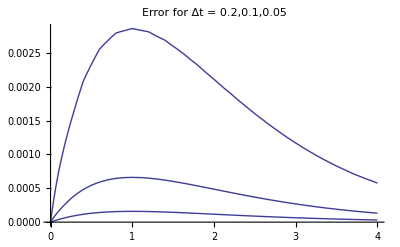

```mathematica
PCsol[0,4,0.2];
p1 = Plot[vPC[t]-vExact[t],{t,0,4}];
PCsol[0,4,0.1];
p2 = Plot[vPC[t]-vExact[t],{t,0,4}];
PCsol[0,4,0.05];
p3 = Plot[vPC[t]-vExact[t],{t,0,4}];
Show[p1,p2,p3,PlotLabel->"Error for Δt = 0.2,0.1,0.05"]
```

Not only is the error much smaller than in Euler's method for the same step size, but the error also decreases much more rapidly as Δt is decreased. The maximum error goes from roughly 0.0029 to 0.0007 to 0.00017 as Δt goes from 0.2 to 0.1 to 0.05.  In other words, the maximum error is reduced by roughly a factor of 4 every time Δt is reduced by a factor of 2. This is exactly what we expect for error that is O(Δt^2).

There are many higher-order methods that are even more accurate than this.  Two the more popular methods are the fourth-order Runge-Kutta method, and the  Bulirsch-Stoer method. These methods will not be discussed here, but  the codes can be found in many other textbooks. See, for instance,  Press et al., (1986).

Also, there are several second-order (and higher-order) methods that require only one force evaluation per timestep. These algorithms can be more efficient when the force evaluation is time-consuming. Three such methods are considered in the exercises: the leapfrog method and a centered-difference method for problems in Newtonian mechanics, and the Adams-Bashforth method for more general problems..

1.4.5 Euler's Method for Systems of ODEs

Consider the general second-order ODE

(ⅆ^2 x)/(ⅆ t^2)=f(t,x,ⅆx/ⅆt),     x(0)=x_o,ⅆx/ⅆt(0)=v_o.

Since the ODE is second-order, Euler's method cannot be used to solve it numerically. However, we can modify the equation so that Euler's method can be used. By introducing a new variable v(t) =ⅆx/ⅆt, Eq. (1.4.13) can be written as the following system of first-order differential equations:

ⅆx/ⅆt=v(t), ⅆv/ⅆt=f(t,x,v),  x(0)=x_o,v(0)=v_o.

Euler's method still does not apply, because it was written originally for a single first-order ODE. However, let us define a vector z(t) = {x(t),v(t)}. Then Eqs. (1.4.14) can be written as a vector ODE:

ⅆz/ⅆt=f(t,z), z(0)=z_o,

where z_o={x_o,v_o} , and the vector function f(t,z) is defined as

f(t,z)={v(t),f(t,x,v)} .

We can now apply Euler's method to this vector ODE, simply by reinterpreting the scalar quantities that appeared in Eq. (1.4.7) as vectors:

z(t_n)=z(t_(n-1))+Δt f(t_(n-1),z(t_(n-1))) .

In fact, there is nothing about Eqs. (1.4.15) and (1.4.17) that limits them to two-dimensional vectors. An Nth-order ODE of the general form given by Eq. (1.2.1) can also be written in the form of Eq. (1.4.15) by defining a series of new variables

v(t)=ⅆx/ⅆt,a(t)=(ⅆ^2 x)/(ⅆ t^2),...,u(t)=(ⅆ^(N-1)x)/(ⅆ t^(N-1)),

a vector

z(t)={x(t),v(t),a(t),...,u(t)},

and a "force"

f(t,z)={v,a,...,u,f(t,x,v,a,...,u)}.

Thus, Euler's method in vector form, Eq. (1.4.17), can be applied to a general Nth-order ODE. Below, we provide the simple changes to the previous module Eulersol that allow it to work for a general ODE of order N:

```mathematica
Clear["Global`*"]
```

```mathematica
Eulersol[z0_,time_,Δt_]:= Module[{t,z,sol},
t[n_] := n Δt;
z[n_] :=z[n]=z[n-1] + Δt  f[t[n-1], z[n-1]];
z[0] :=   z0;
sol = Table[Table[{t[n],z[n][[m]]},{n,0,time/Δt}],{m,1,Length[z0]}];
zEuler = Table[Interpolation[sol[[m]]],{m,1,Length[z0]}];]
```

Thanks to the ease with which Mathematica handles vector arithmetic, the module is nearly identical to the previous scalar version of the Euler method.  In fact, except for renaming some variables, the first four lines are identical.  Only the lines involving creation of the interpolating functions differ. This is because the solution list sol  is created as a table of lists, each of which is a dataset of the form {t[n],z_m[n]}.  Each element of zEuler is an interpolation of a component of z.

To use this module, we must first define a force vector f(t,z). Let's take the case of the 1-D harmonic oscillator problem as an example. In this case z=(x,v), and f = (v,-x) (i.e. ⅆx/ⅆt = v, ⅆv/ⅆt = -x):

```mathematica
f[t_,z_] := {v,-x}/.{x->z[[1]],v->z[[2]]}
```

A delayed equality must be used in defining f; otherwise Mathematica will attempt to find the two elements of z when making the substitution,  and this will lead to an error, since z has not been defined as a list yet.

Taking the initial condition z_o = (1,0) (i.e., x_o = 1, v_o = 0),  in Cell 1.47 we run the Euler code and in Cell 1.48 plot the solution for x(t), which is the first element of zEuler.

```mathematica
Eulersol[{1,0},10,.02]
```

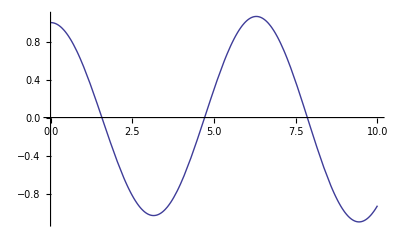

```mathematica
Plot[zEuler[[1]][t],{t,0,10}]
```

The code clearly works, but a keen eye can see that the expected cosine oscillations are actually growing slowly with time, even at the relatively small step size of 0.02.

As already discussed, the Euler method is only first-order accurate. Nevertheless, the general methods discussed in this section also work for higher-order methods, such as the predictor-corrector code of the previous section.  Examples may be found in the exercises at the end of the section.

1.4.6 The Numerical N-Body Problem: An Introduction to Molecular Dynamics

One way that systems of ODEs arise in the physical sciences is in the description of the motion of N interacting classical particles.  Newton  solved this problem for the case of two particles (the two-body problem) interacting via a central force. However, for three or more particles there is no general analytic solution, and numerical techniques are of great importance in understanding the motion.

In the numerical method known as molecular dynamics, the coupled equations of motion for the N particles are simply integrated forward in time using Newton's second law for each particle. There is nothing subtle about this - the numerical techniques learned in the previous sections are simply applied on a larger scale. The subtleties only arise when details such as  error accumulation, code efficiency, and the like must be considered.

Below, we show how to use Mathematica's intrinsic function NDSolve to numerically solve the following N body problem: For particles at positions r_1(t), r_2(t),…, r_N(t), the equations of motion are

m_i (ⅆ^2 r_i)/(ⅆ t^2)=∑_(j=1
j≠i)^N F_(i j)(r_i-r_j),

where F_(i j) is the force between particles i and j,  and m_i is the mass of particle i.  To complete the problem, we must also specify initial conditions on position and velocity :

r_i(0)=r_io ,(ⅆ r_i)/ⅆt=v_io,i=1,...,n

The following module MDsol solves this problem numerically:

```mathematica
Clear["Global`*"]
```

```mathematica
MDsol[z0_,time_] := Module[{},
npart = Length[z0]/6;
r[i_,t_] = {x[i][t],y[i][t],z[i][t]};
v[i_,t_] = {vx[i][t],vy[i][t],vz[i][t]};
Z[t_]=Flatten[Table[{r[i,t],v[i,t]},{i,1,npart}]];
f[t_] = Flatten[Table[{v[i,t],
(Sum[F[i,j,r[i,t]-r[j,t]],{j,1,i-1}]+
Sum[F[i,j,r[i,t]-r[j,t]],{j,i+1,npart}])/mass[[i]]},{i,1,npart}]];
ODEs = Flatten[Table[Z'[t] [[n]]==f[t][[n]],{n,1,6*npart}]];
ics = Table[Z[0][[n]]==z0[[n]],{n,1,6*npart}];
eqns = Join[ODEs,ics];
NDSolve[eqns,Z[t],{t,0,time},MaxSteps->10^5]]
```

To understand what this module does, look at the last line. Here we see that NDSolve is used to integrate a list of equations called eqns, that the equations involve a vector of unknown functions Z[t], and that the equations are integrated from t=0 to t=time.  The definition of Z[t] can be found a few lines higher in the module: it is a list of variables,{r[i,t],v[i,t]}. The ith particle position vector  r[i,t] is defined in the second line as  having components {x[i][t],y[i][t],z[i][t]}, and  the velocity vector v[i,t] has components {vx[i][t],vy[i][t],vz[i][t]}.  These functions use a notation we haven't seen before: the notation x[i][t] means the same thing as x[i,t]. The reason we use the former and not the latter notation is due to a vagary of NDSolve: NDSolve likes to work on functions of one variable; otherwise it gets confused and thinks it is solving a PDE. The notation x[i][t] fools NDSolve into thinking of x as a function of a single argument, the time t.

The Flatten function is used in the definition of Z[t] because NDSolve works only on a simple list of unknown functions, without sublists.

The list eqns can be seen to be a concatenation of a list of ODEs called ODEs and a list of initial conditions called ics. The initial conditions are given as an argument to the module, in terms of a list z_o of positions and velocities for each particle of the form

z_o=Flatten[{r_(1o),v_(1o),r_(2o),v_(2o),...}].

The Flatten command is included explicitly here to ensure that z_o is a simple list, not an array.

The acceleration function f(t) is defined as

f(t)= {v_1,1/m_1∑_(j=2)^N F_(1j)(r_1-r_j),v_2,1/m_2∑_(j=1
j≠2)^N F_(2j)(r_2-r_j),...} ,

and the result is flattened in order for each element to correspond to the proper element in Z.   The fact that the sum over individual forces must neglect the self–force term  j=i requires us to write the sum as two pieces, one from j=1 to i-1, and the other from j=i+1 to N.

The value of N, called npart in the module (because N is a reserved function name),  is determined in terms of the length of the initial condition vector z0, in the first line of the code.

Finally, the module itself is given no internal variables (the internal-variable list is the null set {}), so that we can examine each variable if we wish.

In order to use this code, we must first define a force function F_(i j)(r). Let's consider the gravitational N body problem, where the force obeys Newton's law of gravitation:

F_(i j)(r)=-G m_i m_j r/r^3,

where G=6.67 ×10^-11 m^3/kg s^2.  We can define this force using the command

```mathematica
F[i_,j_,r_] := -mass[[i]] mass[[j]]r/(r.r)^(3/2)
```

Here mass is a length-N list of the masses of all particles, and we have set the gravitational force constant G=1 for simplicity.

Let's apply this molecular dynamics code to the simple problem of two gravitating bodies orbiting around one another. For initial conditions we will choose r_1 = v_1 = 0, and r_2=(1,0,0), v_2 = (0,0.5,0). Thus, the list of initial conditions is

```mathematica
z0 = Flatten[{{0,0,0,0,0,0},{1,0,0,0,0.5,0}}]
```

{0,0,0,0,0,0,1,0,0,0,0.5,0}

Also, we must not forget to assign masses to the two particles. Let's take one mass 3 times that of the other:

```mathematica
mass = {3,1}
```

{3,1}

Now we run the code for 0<t<7:

```mathematica
s=MDsol[z0,7]
```

{{x[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],y[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],z[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],vx[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],vy[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],vz[1][t]→InterpolatingFunction[{{0.,7.}},<>][t],x[2][t]→InterpolatingFunction[{{0.,7.}},<>][t],y[2][t]→InterpolatingFunction[{{0.,7.}},<>][t],z[2][t]→InterpolatingFunction[{{0.,7.}},<>][t],vx[2][t]→InterpolatingFunction[{{0.,7.}},<>][t],vy[2][t]→InterpolatingFunction[{{0.,7.}},<>][t],vz[2][t]→InterpolatingFunction[{{0.,7.}},<>][t]}}

The result is a list of interpolating functions for each component of position and velocity of the two particles.  We can do whatever we wish with these - perform more analysis, make plots, etc.  One thing that is fun to do (but is difficult to show in a textbook)  is to make an animation of the motion. An example is displayed in the electronic version of the book, plotting the (x,y) positions of the two masses at a series of separate times. (As discussed in Chapter 9, the animation can be viewed by clicking the play button in the controls, or moving the slider with the mouse.) Only the command that creates the animation is given in the hard copy, in Cell 1.55.

```mathematica
Manipulate[ListPlot[Table[{x[n][t],y[n][t]}/.%[[1]],{n,1,2}],PlotStyle->PointSize[0.015],AspectRatio->1,PlotRange->{{-.1,1.2},{-.1,1.2}}],{t,0,7,Appearance->"Open"}]
```

Another thing one can do (that can be shown in a textbook!) is plot the orbits of the particles in the x-y plane.  The parametric plots in Cell 1.56 do this, using the usual trick of turning off intermediate plot displays in order to save space:

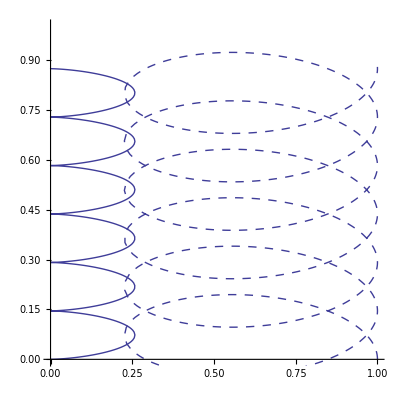

```mathematica
p1=ParametricPlot[{x[1][t],y[1][t]}/.s[[1]],{t,0,7}];
p2=ParametricPlot[{x[2][t],y[2][t]}/.s[[1]],{t,0,7},PlotStyle->Dashing[{0.015,0.015}]];
Show[p1,p2,PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

The mass-1 particle can be seen to move considerably farther in the x-direction than the mass-3 particle, as expected from conservation of momentum. Both particles drift in the y-direction, because  the mass-1 particle had an initial y-velocity, which imparts momentum to the center of mass.

These orbits look a bit more complicated than one might have expected - aren't these two bodies simply supposed to perform elliptical orbits around the center of mass? The answer is yes, but the orbits look different depending on one's frame of reference.  In a frame moving with the center of mass, the orbits do look like closed ellipses (see the exercises).

Of course, the orbits of two gravitating particles can be determined analytically, so there is really no need for molecular dynamics. However, for three or more bodies, no general analytic solution is available, and molecular dynamics is crucial for understanding the motion.

Take, for example, the solar system.  Table 1.2 provides the positions and velocities of the major bodies in the solar system, with respect to the solar system center of mass, on January 1, 2001.  We can use the information in this table as initial conditions to determine the subsequent motion of these planetary bodies.

Table 1.2 : Positions and Velocities of Sun and Planets^a
^aOn  January 1, 2001, 12 noon GMT, with respect to the solar system center of mass
 Data adapted from the Horizon system at JPL

Body | Mass (kg) | x (m) | y (m) | z (m) | vx (m/s) | vy (m/s) | vz (m/s)
Sun | 1.9891×10^30 | -7.0299×10^8 | -7.5415×10^8 | 2.38988×10^7 | 14.1931 | -6.9255 | -0.31676
Mercury | 3.302×10^23 | 2.60517×10^10 | -6.1102×10^10 | -7.3616×10^9 | 34796. | 22185.2 | -1379.78
Venus | 4.8685×10^24 | 7.2129×10^10 | 7.9106×10^10 | -3.0885×10^9 | -25968.7 | 23441.6 | 1819.92
Earth | 5.9736×10^24 | -2.91204×10^10 | 1.43576×10^11 | 2.39614×10^7 | -29699.8 | -5883.3 | 0.050215
Mars | 6.4185×10^23 | -2.47064×10^11 | -1.03161×10^10 | 5.8788×10^9 | 1862.73 | -22150.6 | -509.6
Jupiter | 1.8986×10^27 | 2.67553×10^11 | 7.0482×10^11 | -8.911×10^9 | -12376.3 | 5259.2 | 255.192
Saturn | 5.9846×10^26 | 6.999×10^11 | 1.16781×10^12 | -4.817×10^10 | -8792.6 | 4944.9 | 263.754
Uranus | 1.0243×10^26 | 2.65363×10^12 | -3.6396×10^12 | 1.37957×10^10 | 4356.6 | 3233.3 | -166.986
Neptune | 8.6832×10^25 | 2.2993×10^12 | -1.90411×10^12 | -3.6864×10^10 | 4293.6 | 4928.1 | -37.32
Pluto | 1.27×10^22 | -1.31126×10^12 | -4.2646×10^12 | 8.3563×10^11 | 5316.6 | -2484.6 | -1271.99

This data is also summarized in the following list, which makes it easy to use. Each element in the list corresponds to a column entry in the Table:

```mathematica
sun={1.9891*^30,-7.0299*^8,-7.5415*^8,2.38988*^7,14.1931,-6.9255,-0.31676};
mercury={3.302*^23,2.60517*^10,-6.1102*^10,-7.3616*^9,34796.,22185.2,-1379.78};
venus={4.8685*^24,7.2129*^10,7.9106*^10,-3.0885*^9,-25968.7,23441.6,1819.92};
earth={5.9736*^24,-2.91204*^10,1.43576*^11,2.39614*^7,-29699.8,-5883.3,0.050215};
mars={6.4185*^23,-2.47064*^11,-1.03161*^10,5.8788*^9,1862.73,-22150.6,-509.6};
jupiter={1.8986*^27,2.67553*^11,7.0482*^11,-8.911*^9,-12376.3,5259.2,255.192};
saturn={5.9846*^26,6.999*^11,1.16781*^12,-4.817*^10,-8792.6,4944.9,263.754};
neptune={8.6832*^25,2.2993*^12,-1.90411*^12,-3.6864*^10,4293.6,4928.1,-37.32};
uranus={1.0243*^26,2.65363*^12,-3.6396*^12,1.37957*^10,4356.6,3233.3,-166.986};
pluto={1.27*^22,-1.31126*^12,-4.2646*^12,8.3563*^11,5316.6,-2484.6,-1271.99};
```

```mathematica
solarsys = {sun,mercury,venus,earth,mars,jupiter,saturn,uranus,neptune,pluto};
```

Let's use this data to try to answer the following important question: is the solar system stable? How do we know that planetary orbits do not have a nonzero Lyapunov exponent, so that they may eventually fly off their present courses, possibly colliding with one another or with the sun?

There has naturally been a considerable amount of very advanced work on this fundamental problem of celestial mechanics. Here, we will simply use our molecular dynamics algorithm to solve for the orbits of the planets, proving the system is stable over the next three hundred years. This is not very long compared to the age of the solar system, but it is about the best we can do using Mathematica unless we are willing to wait for long times for the code to complete.  More advanced numerical integrators, run on mainframe computers, have evaluated  the orbits over much longer time periods.

Because the inner planets are small and rotate rapidly about the sun , we will ignore Mercury, Venus, and Earth  in order to speed up the numerical integration.

First we input the data for the sun and the outer planets into the mass list:

```mathematica
mass = Join[{sun[[1]]},Table[solarsys[[n]][[1]],{n,5,Length[solarsys]}]]
```

{1.9891×10^30,6.4185×10^23,1.8986×10^27,5.9846×10^26,1.0243×10^26,8.6832×10^25,1.27×10^22}

Next,  we create a list of initial conditions:

```mathematica
z0 = Flatten[Join[Table[sun[[j]],{j,2,7}],Table[Table[solarsys[[n]][[j]],{j,2,7}],{n,5,Length[solarsys]}]]];
```

Finally, we define the force , this time keeping the correct magnitude for G:

```mathematica
G= 6.67 10^-11;
```

```mathematica
F[i_,j_,r_] := -G mass[[i]] mass[[j]]r/(r.r)^(3/2)
```

We now run the molecular dynamics code for the planet positions forward in time  for 300 years.

```mathematica
solution1 = MDsol[z0,300*365*24*3600];
```

This takes quite some time to run, even on a fast machine. In Cell 1.65 we plot the orbits in 3D with a parametric plot.

```mathematica
orbits=Table[{x[n][t],y[n][t],z[n][t]}/.solution1[[1]],{n,1,7}];
```

```mathematica
ParametricPlot3D[orbits,{t,0,3 10^2 365 24 3600},PlotLabel->"Orbits of the outer planets for 300 years",PlotRange->All]
```

-Graphics3D-

Evidently, the outer planets are stable, at least for the next 300 years!    (If nothing else, this plot shows the huge scale of the outer planet's orbits compared to that of Mars, the innermost orbit in the plot. Earth's orbit would barely even show up as a spot at the center. Distances are in meters.)

Exercises for Sec. 1.4

(1) The drag force F on a blunt  object moving through air is not linear in the velocity v except at very low speeds. A more realistic model for the drag in the regime where the wake is turbulent is F=-c v^2 Sign(v), where c is a constant proportional to the cross-sectional area of the object and the mass density of air. If we use this model for the drag force in the problem of a man throwing a pebble vertically [c.f. Sec. 1.3, Exercise (4)] , the equation for the height is now nonlinear:

(ⅆ^2 y)/(ⅆ t^2)+c/m(ⅆy/ⅆt)^2 Sign(ⅆy/ⅆt)=-g.

(a) Solve this equation numerically using NDSolve, and plot the solution. Take m = 1 kg,  c = 1 kg /m, y(0) = 0, and v(0) = 6 m/s.

(b) Numerically determine the maximum height, and the time required for the rock to fall back to y(0).

(2) Use NDSolve to find the trajectories x(t) and x'(t) for the Van der Pol oscillator, which satisfies Eq. (1.2.20), for initial conditions (x,x')=(1,1),(0.1,0.3), and (3,2)  and 0<t<20. Use a parametric plot to plot the trajectories in phase-space (x,x'). Note how the trajectories converge onto a single curve, called a limit cycle. [See Sec. 1.2 Exercise (6), for the direction field associated with this oscillator.]

(3) Ming the Merciless drops Flash Gordon out the back of his spaceship (in a spacesuit, fortunately). The evil Ming has contrived to leave Flash initially motionless with respect to the earth, whose surface is 5,000 km below. Use Newton's 1/r^2 force law and NDSolve to determine how long Flash has to be rescued before he makes a lovely display in the evening sky. (Hint: M_earth = 5.98 × 10^24 kg. The radius of the earth is roughly 6,370 km, and the height of the atmosphere is about 100 km.  The gravitational constant is G = 6.67×10^-11 N m/kg^2. Remember that the 1/r^2 force is measured with respect to the center of the earth.)

(4) Einstein's general theory of relativity generalizes Newton's theory of gravitation to encompass the situation where masses have large kinetic and/or potential energies (on the order of or larger than their rest masses). Even at low energies, the theory predicts a small correction to Newton's 1/r^2 force law:

f(r)=-G M(1/r^2+(3 L^2)/(c^2 r^4)),

where L is the specific angular momentum-- see Eq. (1.2.22). This force per unit mass replaces that which appears on the right-hand side of the orbit equation (1.3.5).

(a)Use NDSolve to determine the new orbit r(θ) predicted by this equation, and plot it for 0<θ < 4π, taking orbital parameters for the planet Mercury: r(0) =  46.00×10^6 km, (perihelion distance) r'(0)=0,  L = 2.713×10^15 m^2/s. The mass of the sun is 1.9891×10^30 kg.

(b) Show numerically  that the orbit no longer closes, and that each successive perihelion precesses by an amount Δθ . Find a numerical value for Δθ.   Be careful: the numerical integration must be performed very accurately! (The precession of Mercury's perihelion has been measured, and after successive refinements, removing extraneous effects, it was found to be in reasonable agreement with this result.)

(5) A cubic cavity has perfectly conducting walls of unit length, and supports electromagnetic standing waves. The magnetic field in the modes (assumed to be TE modes) is

B_(l m n)(x,y,z)=B_o{-l/(l^2+m^2)sin(l π x) cos(m π y)cos(n π z),-m/(l^2+m^2)cos(l π x) sin(m π y)cos(n π z),cos(l π x) cos(m π y) sin(n π z)}.

For (l,m,n) = (1,1,1) solve Eqs. (1.2.24) numerically for the field lines r(s,r_o), for -2<s<2 and initial conditions r_o={0.25 i,0.25 j, 0.25 k}, i,j,k,=1,2,3. Use ParametricPlot3D to plot and superimpose the solutions. [The solution is shown in Fig. 1.12 for the mode with  (l,m,n) =(1,2,1).]

-Graphics3D-

Fig. 1.12 Magnetic field lines  in a TE(1,2,1) cavity mode.

(6)  Repeat the calculation of the Lyapunov exponent done in the text, but for an integrable system, the one-dimensional undamped harmonic oscillator, with dimensionless Hamiltonian H=(v^2 + x^2)/2,  taking the initial condition x=0, v = 1.  What happens to λ(t), the right-hand side of Eq. (1.4.2), at large times?

(7) Not all trajectories of a chaotic system have positive Lyapunov exponents. Certain regions of phase-space can still be integrable, containing nested curves upon which the orbits lie.  Take, for example, our chaotic system described by Eq. (1.4.1) with the same parameter values as discussed before, (V_o = V_1 = k_o = k_1 = m =1, ω =2), but a different initial condition, x(0) = 3, v(0) = 3.  Repeat the evaluation of the Lyapunov exponent for this trajectory, again taking 40 adjacent trajectories with |d_o| < 10^-5 and 0<t<50.

(8) Hamiltonian systems are not the only systems that exhibit chaotic motion. Systems that have dissipation can also exhibit chaos. The fact that these systems no longer conserve phase-space volume implies that orbits can collapse onto weirdly-shaped surfaces called strange attractors.  Although motion becomes confined to this attracting surface, motion within the surface can be chaotic, exhibiting a positive Lyapunov exponent. The Lorenz system of ODEs is an example of a dissipative chaotic system with a strange attractor.  This system models an unstable thermally convecting fluid, heated from below. The equations for the system are three coupled ODEs for functions x(t),y(t), and z(t), (which are a normalized amplitude of convection, a temperature difference between ascending and descending fluid, and a distortion of the vertical temperature profile from a linear law, respectively):

ⅆx/ⅆt=σ(y-x),
ⅆy/ⅆt=r x-y-x z,
ⅆz/ⅆt=x y-b z,

where σ , b, and r are constants. For sufficiently large r,  this system exhibits chaos.

(a) Taking characteristic values of σ=10, b=8/3, and r = 28,  integrate the Lorenz equations for 0<t<100. Take as an initial condition x=1,y=15,z=10. Use the function ParametricPlot3D to plot the (x(t),y(t),z(t)) orbit .  This orbit will exhibit the strange attractor for this dissipative dynamical system. (Hints: To integrate for the required length of time you will need to increase the MaxSteps option in NDSolve to around 10,000 or so. Also, after plotting the strange attractor, it is fun to rotate it and view it at different angles. See the discussion of real-time 3D graphics in Chapter 9. You will need to increase the number of plot points used in the parametric plot.)

(b) Repeat part (a) using higher accuracy, by taking AccuracyGoal and PrecisionGoal in NDSolve to their highest possible values for your computer system. Plot the displacement between the two trajectories as a function of time. Does this system exhibit the explosive growth in error characteristic of chaos?

(c) Calculate the Lyapunov exponent for this trajectory by plotting the right-hand side of Eq. (1.4.2) for  0<t<15. [Now z = (x,y,z) in Eq. (1.4.2).] Average over 20 nearby trajectories with  |d_o| < 10^-5.

The solution to part a) is shown  in Fig. 1.13 (this plot can be viewed from different angles by dragging on it using  the mouse):

-Graphics3D-

Fig. 1.13 Strange attractor for the Lorenz system.

(9) Magnetic and electric field lines can also display chaotic behavior.  For example, consider the following simple field:

B_o(r,θ,z)=2 r r̂ Sin(2θ)  +θ̂ ( r^3/4+2 r Cos(2θ) ) + ẑ.

[One can easily show that this field satisfies ∇·B=0. It consists of a uniform field superimposed on a quadrupole field created by external currents,  and the field from a current density j(r)∝r^2 ẑ.]
For this field is it useful to consider field line ODEs of the form

ⅆr/ⅆz=(ⅆr/ⅆs)/(ⅆz/ⅆs)=B_r(r,θ,z)/B_z(r,θ,z) and rⅆθ/ⅆz=(rⅆθ/ⅆs)/(ⅆz/ⅆs)=B_θ(r,θ,z)/B_z(r,θ,z).

[see Eqs. (1.3.6)].

(a) Solve these coupled ODEs for r(z) and θ(z) using NDSolve, and  plot the resulting field line in (x,y,z) via ParametricPlot3D  for 0<z<20 and for initial conditions  θ_o=π / 2, and r_o= -5 + 2 n , n=0,1,2,3,4. [Hint:  Along the field line x(z)=r(z) cosθ(z), y(z)=r(z) sinθ(z).]

(b) Although the result from part (a) appears to be very complicated, these field lines are not chaotic. One way to see this is to project the field lines into the (x,y) plane, since the field is independent of z. Do so, and show that the field lines created in part (a) fall on nested closed curves.   (The solution is shown in Fig. 1.14. Note the appearance of two magnetic islands, around which the field lines spiral. )

Fig. 1.14 Solution to Exercise (8)(b): Field lines for the magnetic field B_o, projected into the (x,y) plane.

(c) A chaotic magnetic field can be created by adding another magnetic field to B_o, writing B_s(r,θ,z)=B_o(r,θ,z) +ϵ ( r̂  r sin(θ-z) + θ̂ 2r cos(θ-z)). (This field also satisfies  ∇·B=0.)  For ϵ=1/3 replot the field lines for this field in (x,y,z), using the same initial conditions as in  part (a).The  field lines now become a "tangle of spaghetti".   Project them into the (x,y) plane. You will see that some of the field lines wrap around one magnetic island for a time, then get captured by the adjoining island. This complex competition between the islands is responsible for the chaotic trajectory followed by the lines.

(d) One way to test visually whether some of the field lines are chaotic is to note that the magnetic field B_s(r,θ,z) is periodic in z with period 2 π.  If B_s were  not chaotic, it would create field lines that fell on closed surfaces,  and the  surfaces would also have to be periodic in z. Therefore, if you plot  values of (r(z_n),θ(z_n)) for z_n=2 π n in either the (r ,θ) plane or the (x, y) plane, the resulting points must form closed curves  for a nonchaotic field.  This is called a Poincaré plot. However, for  a chaotic field the field lines are not on closed surfaces; rather,  they fill space.  A Poincaré  plot will now show a chaotic collection of points filling a region in the (r ,θ) plane [or the (x , y) plane].

For the same initial conditions as in part (a), use NDSolve to evaluate the field lines for the field B_s for ϵ=1/3 and  0≤ z≤ 400 π. (Increase MaxSteps to about 200000) . Make a table of values of (r(z_n),θ(z_n)) for z_n=2 π n. Use ListPlot to plot these values in the (x,y) plane.  (The solution is shown in Fig. 1.15 for ϵ=1/4)

Fig. 1.15 Solution to Exercise(8)(d): Poincaré plot in the (x,y) plane for the magnetic field B_sfor ϵ=1/4 .

(10) Use Euler's method to

(a) solve the following ODEs with initial conditions over the given range of time, and for the given step size. Then,

(b) plot the solution;

(c) solve the ODE analytically, and plot the error in x(t);

(d) using the results of (c) predict how small a step size is necessary for the error to be smaller than 10^-4 over the course of the run.

(i)	ⅆx/ⅆt=sin(t)-x, x(0)=1, 0<t<5,   Δt=0.1.

(ii)	4 x+ⅆx/ⅆt+(ⅆ^2 x)/(ⅆ t^2)==0,  x(0)=2,x'(0)=1, 0<t<10, Δt=0.01.

(iii)	x'''+2 x''+x'+2x=cos t  x(0)=x'(0)=x''(0)=0, 0<t<20, Δt=0.02.

(11) Use Euler's method to solve the following nonlinear ODE initial-value problems, and answer the questions concerning the solutions. By looking at solutions as you vary the step size , ensure that each answer is accurate to at least 10^-4.

(a)   x'(t)=t/(x+t)^2,x(0)=3 .  What is x(10)?

(b)    x''(t)=cos(t)cos(x),  x(0)=-1,  x'(0)=0. What is x(20)?

(c) Eqs. (1.4.25), σ=10, b=8/3,  and r = 28; x(0)=y(0)=z(0)=1. What are x(3) and x(20)?

(12)  Prove that the error in the integral of Eq. (1.4.6) is of 0(Δt^2). (Hint: Taylor-expand f about the initial time.)

(13)  Prove that the error in the integral of Eq. (1.4.10) is of 0(Δt^3).

(14) Modify our second-order predictor-corrector algorithm so that it can handle differential equations of order higher than one, or systems of coupled equations. Use the modified method to repeat

(a) Exercise (10)(ii),

(b) Exercise (10)(iii),

(c) Exercise (11)(b),

(d) Exercise (11)(c).

(15) Centered-difference method. The following discretization method can be used to solve a second-order differential equation of the form (ⅆ^2 x)/(ⅆ t^2)=f(x,t) , with initial condition x(0)=x_o, x'(0)=v_o. The method requires only one force evaluation per timestep. First, discretize time in the usual way, with t_n = nΔt.  Approximate the second derivative as

(ⅆ^2 x)/(ⅆ t^2)(t_n)=(x(t_(n+1))-2 x(t_n)+x(t_(n-1)))/Δt^2.

This approximation is referred to as a centered-difference form for the derivative, since the expression is symmetric about timestep t_n . (See the Appendix and Sec. 2.4.5, Table 2.4.)  The differential equation then becomes the recursion relation

x_(n+1)-2 x_n+x_(n-1)=Δt^2 f(x_n,t_n), n>1.

Note that in order to determine the first step,  x_1 , given the initial condition x_o, Eq. (1.4.27) requires x_-1, which is not defined. Therefore, we need a different equation to obtain x_1. Use

x_1=x_o+Δt v_o+Δt^2/2 f(x_o,t_o) ,

which is the formula for position change due to a constant acceleration.

(a) Write a module that implements this scheme.

(b) Use this module to solve the problem of a harmonic oscillator, with f=-x, taking x_o = 1, and v_o =  0 on the interval 0<t<20, and taking Δt = 0.1. Plot the error in your solution, compared to the analytic solution cos t.

(c) Repeat (b) with Δt = 0.02. By what factor has the error been reduced? What is the order of this method?

(16) The leapfrog method. The following discretization method can also be used to solve a second-order  differential equation of the form (ⅆ^2 x)/(ⅆ t^2)=f(x), with initial conditions x(0)=x_o,x'(0)=v_o. This method requires only one force evaluation per timestep. We first write this equation in terms of two first-order equations for position and velocity:

ⅆx/ⅆt = v(t), ⅆv/ⅆt = f(x).

We then discretize x(t) on a grid t_n=n Δt. But we discretize the velocity v(t) on the grid t_(n+1/2)=(n+1/2) Δt. 
In each case  we use centered-difference  forms for the discretized first derivative:

(v_(n+1/2)-v_(n-1/2))/Δt=f(x_n),
(x_n- x_(n-1))/Δt=v_(n-1/2).

In the first equation, the derivative of v is evaluated at timestep n using a centered-difference form for ⅆv/ⅆt(t_n).  (See the Appendix and Sec. 2.4.5, Table 2.4.) In the second equation, the derivative of x is evaluated at timestep n-1/2, using the same centered-difference form.  The method is started using a predictor-corrector step in order to obtain v_(1/2) from x_o and v_o:

x_(1/2) = x_o + v_o Δt/2 ;
v_(1/2)= v_o + 1/2(f(x_o) + f(x_(1/2))) Δt/2.

(a) Write a module that implements this scheme.

(b) Use the module to solve  the same problem as in Exercise (15)(b) and (c). What is the order of this method?

(c) The leapfrog method evaluates the velocity at half-integer timesteps, and the position at integer timesteps. An equivalent method  (the Störmer-Verlet method) can be written that evaluates both velocity and position at integer timesteps, by breaking the velocity step into two half-steps:
		v_(n-1/2)=v_(n-1)+Δt/2 f(x_(n-1)),
x_n=x_(n-1)+ Δt v_(n-1/2,)
v_n=v_(n-1/2)+Δt/2 f(x_n).

(i) Show that this method is equivalent to the leapfrog method. (Hint: advance the timestep in the first equation by one step.)
		(ii) Show that the Jacobian of the transformation from (x_(n-1),v_(n-1)) to (x_n,v_n) equals one. This implies that the Störmer-Verlet method conserves phase space area (see Sec. 1.2.2). (This is a simple example of a class of phase space area-preserving methods referred to as symplectic integrators. Such integrators are especially useful for numerically integrating Hamiltonian systems.)

(17) The Adams-Bashforth method. Consider the following general first-order ODE (or system of ODEs): ⅆv/ⅆt=f(v,t), with initial condition v(0)=v_o. We wish to obtain a second-order (or even higher-order) method for solving this problem, using only one force evaluation per step.  First, we replace Eq. (1.4.11) by

v(t_n)=v(t_(n-1))+Δt f(t_(n-1/2),v(t_(n-1/2)))+0(Δt^3).

This formula is exact if f is a linear function of time, as is clear from Fig. 1.11.

(a) Show that the error in one step is in fact of order Δt^3.

(b) To obtain the force at the intermediate time t_(n-1/2), we extrapolate from previous force evaluations. If at timestep t_n we call the force  f_n, then by using a linear fit through f_(n-1) and f_(n-2) show that

f_(n-1/2)=( 3 f_(n-1) - f_(n-2))/2.

(c) The code arising from this approach is called the second-order Adams-Bashforth method.   It is

v(t_n)=v(t_(n-1))+Δt ( 3 f_(n-1) - f_(n-2))/2 .

This algorithm is an example of a multistep method, where force evaluations from previous steps are kept in memory and used to make the next step. One way to save previous force evaluations is to use the double-equal sign trick : define a function force[n_] := force[n] = f(t_n,v(t_n)), and use this function in Eq. (1.4.29).  Write a module for this algorithm. To take the first step, use the second-order predictor-corrector method.  Use your module to solve the coupled system

ⅆx/ⅆt = - y - x,  ⅆy/ⅆt = 2 x-3 y + sin t

for 0<t<10, taking Δt = 0.1, with initial conditions x(0)=0,y(0)=1 . Compare y(t) with the exact solution found using DSolve, and verify that the method is second-order accurate by evaluating the error taking half the step size, then reducing by half again.

(18) For force laws that are derivable from a potential, such as the gravitational force, the equations (1.4.21)  are Hamiltonian in form, with conserved energy

H=∑_(i=1)^N(m_i v_i^2)/2+∑_(i=1)^N ∑_(j=i+1)^N V_(i j)(r_i-r_j),

where V_(i j) is the potential energy of interaction between particles i and j. Evaluating the energy in molecular dynamics calculations provides a useful check of the accuracy of the numerics.  This Hamiltonian also conserves total linear momentum,

P=∑_(i=1)^N m_i v_i

For central-force problems where the potential energy depends only on the distance between bodies (again, gravity is an example), the total angular momentum L = (L_x,L_y,L_z)  is also conserved, and provides three more useful checks on the numerical accuracy of a code:

L=∑_(i=1)^N m_i r_i×v_i.

(a)Run the example problem on two gravitating bodies (see Cell 1.56). Use the results to calculate and plot the energy, the total momentum, and the z-component of angular momentum as a function of time.

(b) Repeat (a), setting  AccuracyGoal and PrecisionGoal to their highest possible values for your computer system.

(c) The center-of-mass velocity is defined as V_cm=P/∑_(i=1)^N m_i. Plot the orbits of the two planets as seen in a frame moving at the constant speed V_cm. What do they look like in this frame of reference?

(19) A classical model of a helium atom consists of a massive nucleus with mass roughly 4 m_p (m_p being the proton mass) and charge 2e, and two electrons with mass m_e and charges -e.  In this model the electrons are equidistant from the nucleus, on opposite sides, and the electrons move in circular orbits. The charges interact via Coulomb's law, written below for charges q_i and q_j separated by displacement r:

F_(i j)(r)=q_i q_j r/(4π ϵ_o r^3).

(a) Analytically solve for an equilibrium distance d(v) of each electron from the nucleus, as a function of the orbital speed v. The orbital period of this motion is T = 2π d/v.

(b) We will numerically examine the stability of this equilibrium. Choose any value of the orbital speed v that you wish. Move the electrons a small distance, 0.05 d(v), in a random direction from the equilibrium determined in part (a). Numerically evaluate the resulting motion for a time 5T and make a movie of the (x,y) motion, plotting every 0.1T. Is this motion stable (i.e., do the electrons remain near the equilibrium orbit)?

(c) Repeat for a displacement from equilibrium of 0.3 d(v).

(d) Repeat (a), (b), and (c) for lithium, nuclear charge 3e, nuclear mass 7m_p. The equilibrium now consists of three electrons arranged in an equilateral triangle around the nucleus.

(20) The great mass of the sun compared to that of the planets is essential to the long-term stability of the solar system.  By integrating the solar system equations four times for 1000 years, keeping the initial positions of the outer planets the same in each case, but taking larger masses for the planets by factors of 10 in each consecutive run, determine roughly how massive the sun must be, as a muliple of that of Jupiter,  in order to provide a stable equilibrium for outer-planet orbits over 10^3 years.  Perform the integration only for the outer planets, from Jupiter on out.  (Take care to check whether NDSolve is giving accurate results over this long time period.)

(21) An astronomer discovers that a minor  asteroid has been kicked through a collision into an unusual orbit. The asteroid is initially located somewhere between Mars and Jupiter, and  is heading at rather high speed into the inner solar system. As of January 1 , 2001 at 12 noon, the asteroid has velocity (11060, -9817, -744) m/s and  position (-5.206× 10^11 , 3.124 ×10^11, 6.142 ×10^10) m (with respect to the solar system center of mass). Using the data of Table 1.2 and the molecular dynamics code, determine which planet this asteroid is going to strike by making a movie of the x-y positions of all solar system bodies in Table 1.2  over a 2-year period, including the asteroid.

(22)(a) Modify the molecular dynamics code to allow for a drag force, so that equations of motion are of the form

m_i (ⅆ^2 r_i)/(ⅆ t^2)=∑_(j=1
j≠i)^N F_(i j)(r_i-r_j)-m_i γ (ⅆ r_i)/ⅆt.

(b) The Lennard-Jones potential is often used to model interatomic interactions classically. The form of the potential energy is V(r)=ϵ(1/(r/a)^12-2/(r/a)^6) , where a  is a distance scale and ϵ is an energy scale. We are going to use molecular dynamics to determine the form of molecules that interact via the Lennard-Jones potential. To do so, start with N atoms distributed randomly in a cube with sides of length N^(1/3).   Take a = m=ϵ = 1.   Initially the atoms have zero velocities. Add some (small) damping to the motion of the atoms, and follow their motion until they fall into a minimum energy state.

(i) Construct the energy function. Then, taking γ = 0.05,   and  for N = 3,4,5,6,

(ii) follow the motion for 0<t<100.

(iii) Evaluate and plot  the energy vs. time.  Does it appear that an energy minimum has been achieved? For each N-value, what is the minimum energy in units of ϵ?

(iv) Use ParametricPlot3D to plot the positions of the atoms. Can you describe the structure in words?

(v) If a minimum has not yet been achieved, repeat the process using the final state of the previous simulation as the new initial condition.

(vi) The larger the molecule, the more local minimum-energy states there are. For N = 5 and 6, repeat your simulations for five different random initial conditions to see if you can find any other minimum energy states. How many did you find?

(23) Modify the molecular dynamics code to be able to handle applied magnetic and electric fields B(r,t) and E(r,t), and a damping force: The equations of motion are now
		(ⅆ^2 r_i)/(ⅆ t^2)=∑_(j=1
j≠i)^N F_ij(r_i-r_j)+q_i(E(r_i,t)+v_i×B(r_i,t))+ m_i γ ẑ (ⅆ z_i)/ⅆt
(The damping is allowed to work only on the z-motion.)

(a) Check that your new molecular dynamics code works by solving numerically for the motion of a single particle in a uniform electric and magnetic field E=(1,0,0), B=(0,0,1), taking m=q=1, γ = 0, and r = v = 0 at t=0. Compare the numerical result from 0<t<10 with the analytic result of  Sec. 1.3, Exercise (6).

(b) A Penning trap is a trap for charged particles, which can hold the particles in vacuum, away from solid walls, using only static electric and magnetic fields. The trap works for particles that all have the same sign of charge. We will take all the charges to have charge 1 and mass 1, so that their potential interaction is  V(r) = 1/r.  The trap has the following applied electric and magnetic fields:

B=(0,0,5), E = (x/2, y/2, -z).
Consider four ions  given random initial x, y, and z velocities in the ranges -0.1 to 0.1, and positions (0,0,1/4), (1,0,0),(-1,0,0),(0,1,0). Their z-motion is damped (using lasers) with rate γ = 0.1. (Only the z-motion is damped; otherwise the ions would be lost from the trap because of the applied torque from the damping). Numerically integrate the motion of these ions until they settle into an equilibrium configuration. What is this configuration?  (Hint: make x -y images of the ion positions. The equilibrium will actually rotate at a constant rate around the origin due to the E×B drift [Sec. 1.3, Exercise (6)].

(24) Consider a model of an elastic rod as a system of masses and springs.  The equilibrium of such a system is considered in Sec. 9.10, Exercises (5) and (6), and is examined using an analytic model in  Sec. 1.5, Exercise (1). Here we will examine the dynamics of this elastic rod, using the molecular dynamics method.  We will consider a system of M=41 masses. In the absence of gravity, the  masses are arranged in equilibrium positions R_i , which are the same as in the statics problem of Sec. 9.10, Exercise (5):

```mathematica
p=a{1/2,0}; q=a{0,Sqrt[3]/2};
R[i_] = (i-1) p + Mod[i,2] q;
```

As before, nearest neighbor masses i and j interact via the isotropic  force

```mathematica
F[i_,j_, r_] := -k[i,j] (r -a  r/Sqrt[ r.r])
```

The total force on mass i is given by interactions with its four nearest neighbors, assuming that the mass is not at the ends of the rod:

```mathematica
Ftot[i_] := {0,-m g} +   F[i,i-2,r[i,t]-r[i-2,t]]+F[i,i-1,r[i,t]-r[i-1,t]] +F[i,i+1,r[i,t]-r[i+1,t]] + F[i,i+2,r[i,t]-r[i+2,t]]
```

where r_i(t) is the position of the ith mass. The end masses are fixed to the walls:

```mathematica
r[1,t_] = R[1];
r[2,t_] = R[2];
r[M,t_] = R[M];
r[M-1,t_] = R[M-1];
```

Modify the molecular dynamics code to handle this type of nearest neighbor force, and solve the following problem: r_i(t=0)=R_i, and v_i(t=0)=0, for m=1,g=0.5, k_(i j)=160, over the time range 0<t<24. [An analytic approach to  a similar problem can be found in  Sec. 4.2, Exercise (7).]

(25) Use the molecular dynamics code and the data in Table 1.2 to plot the x-y velocities of the sun, (v_x(t), v_y(t)),  as a parametric plot over the time range 0<t< 30 years. What is the magnitude of the maximum speed attained by the sun? This oscillatory motion has been discerned in distant stars through tiny oscillatory Doppler shifts in the starlight, providing indirect evidence for the existence of planetary systems beyond our own solar system [Marcy and Butler, (1998)].

## 1.5 Boundary-Value Problems

1.5.1 Introduction

In order to determine a unique solution to an initial-value problem for an Nth-order ODE, we have seen that N initial conditions must be specified. The N initial conditions are all given at the same point in time.

Boundary-value problems differ from initial-value problems in that the N conditions on the problem are provided at more than one point.  Typically they are given at starting and finishing points at, say, t = 0 and t =T.

As a simple example of a boundary-value problem,  consider trying to hit a moving object with an arrow.  To further simplify the problem, let's assume that the arrow moves in a single dimension, vertically, under the influence only of gravity- no air drag or other forces will be kept. Then the position of the arrow, y(t), satisfies

(ⅆ^2 y)/(ⅆ t^2)=-g,

where g = 9.8 m/s^2 is the acceleration of gravity. The arrow starts at y=0 at time t=0, and must be at y=H at t=T in order to hit an object that passes overhead at that instant.  Therefore, the boundary conditions  on the problem are

y(0) = 0, y(T) = H

In order to solve this problem, consider the general solution of Eq. (1.5.1), determined by integrating the ODE twice :

y(t)=C_1+C_2 t-(g t^2)/2.

We determine the constants C_1 and C_2 using the boundary conditions (1.5.2). Since y(0) = 0, Eq. (1.5.3) evaluated at t=0 implies that C_1 = 0. Since y(T) = H, we find that  C_2= H/T + g T / 2,  yielding the following solution for y(t):

y(t)=(H/T+(g T)/2)t-(g t^2)/2.

Finding the solution of this boundary-value problem seems to be no different than finding the solution of an initial-value problem. However, there is a fundamental difference between these two types of problems: unlike solutions to initial-value problems that satisfy the conditions of Theorem 1.1,

The solutions to boundary-value problems need not exist, and if they exist they need not be unique.

It is easy to find examples of boundary-value problems for which there is no solution. Consider the motion of a harmonic oscillator, whose position satisfies

(ⅆ^2 x)/(ⅆ t^2)=-ω_o^2 x.

Let's again try to hit a passing object with this oscillator (an arrow attached to a spring?). The object is assumed to pass through the point x_o at a time t = π/ω_o. Starting the oscillator from the origin at t =0, the boundary conditions are

x(0)=0, x(π/ω_o)=x_o.

Using the first boundary condition in the general solution, given by Eq. (1.1.7), implies that C_1 = 0 and  x(t)=C_2 sin(ω_o t). Now it seems like a simple task to find the value of C_2 using the second boundary condition, as we did in the previous example. Unfortunately, however, we are faced with a dilemma: at the requested time π/ω_o ,

x(π/ω_o)=C_2 sin π=0

for all values of C_2, so it is impossible to satisfy the second boundary condition.  Therefore, there is no solution to this boundary-value problem.

It is also easy to find boundary-value problems for which the solution is not unique. Consider again the previous harmonic oscillator problem, but this time take boundary conditions

x(0)=0, x(T)=0,

for some given time T : that is, we want the oscillator to pass back through the origin at time T. Now, for most values of T, there is only one solution to this problem: the trivial solution x(t) = 0, where the oscillator is stationary at the origin for all time. However, for special values of T there are other solutions. If T = n π / ω_o,  for some integer n, the solution

x(t)=C_2 sin(ω_o t)

matches the boundary conditions  for any value of C_2. Therefore, for these special values of T, the solution is not unique - in fact, there are an infinite number of solutions, corresponding to sine oscillations with arbitrary amplitude given by Eq. (1.5.9).

Another way to do this problem is to hold the time T fixed and instead allow the parameter ω_o to vary. For most values of ω_o,  the boundary conditions (1.5.8) are satisfied only for the trivial solution x(t) = 0. But at values of ω_o  given by

ω_o=n π/T,

the solution again is of the form of Eq. (1.5.9) with arbitrary amplitude C_2.

The problem of determining the values of a parameter (such as ω_o) for which nontrivial (i.e. nonzero) solutions of a boundary-value problem exist is referred to as an eigenvalue problem.

These problems are called eigenvalue problems because, as we will see, they are often equivalent to finding the eigenvalues of a matrix. (See Sec. 6.3). Eigenvalue problems turn out to be very important in the solution of linear PDEs, so we will return to a discussion of their solution in later chapters.

1.5.2 Numerical Solution of Boundary-Value Problems: The Shooting Method

For the simple cases discussed above, general analytic solutions to the ODEs could be found, and the boundary-value problem could be solved analytically (when the solution existed). However, we have already seen that there are many ODEs for which no general analytic solution can be found. In these cases numerical methods must be employed. This section will consider one method that can be used to find a numerical solution to a boundary-value problem: the shooting method.

As an example of the shooting method, consider a general second-order ODE of the form

(ⅆ^2 y)/(ⅆ t^2)=f(t,y,ⅆy/ⅆt)

and with boundary conditions

y(t_o)=y_o,y(t_1)=y_1.

We require the solution for y(t) between the initial time t_o and the final time t_1. An example of such a problem would be our previous archery problem, but with an acceleration determined by the function f.

In attempting to solve this problem numerically, we run into an immediate difficulty. All of the numerical methods that have been described so far in this book have dealt with initial-value problems, where for given initial conditions, we take steps forward in time until the final time is reached. Here we don't know all of the required initial conditions, so we can't step forward in time. Although we are given y(t_o), we don't know y'(t_o). NDSolve, Euler's method, and the predictor corrector method all require the initial position and velocity in order to integrate this problem forward in time.

The shooting method proposes the following solution to this difficulty: if you don't know all of the initial conditions, have a guess! Using the guess, integrate the solution forward, and see if it matches the second boundary condition. If it misses, adjust the guess and try again, iterating until the guess gives a solution that does match the second boundary condition.

You can see immediately why this is called the shooting method: we are shooting an arrow, refining our guesses for the initial velocity until we make a hit at the required instant.

To do this problem in Mathematica, we will first define a function Sol[v0], which solves the initial-value problem taking y'(t_o)=v_o:

```mathematica
Sol[v0_]:=NDSolve[{y''[t]==f[t,y[t],y'[t]],y[t0]==y0,y'[t0]==v0},y,{t,t0,t1}]
```

The result of evaluating this cell is an InterpolatingFunction that gives a solution for the chosen initial velocity v0. In the second argument of NDSolve, we have specified that the unknown function is y rather than y(t), so that the output will be in terms of a pure function. We will see that this slightly simplifies the code for the shooting method.

To see an example, we must first define the function f and chose an initial time and position. Let us take for our example the problem of an arrow shot in the vertical direction, adding  a drag force due to air on the motion of the arrow. The acceleration of the arrow is taken as

```mathematica
f[t_,y_,v_]:=-g-γ v;
g=9.8; γ=0.1;
```

We are working in units of meters and seconds. The added acceleration due to air drag is assumed to be a linear function of the velocity, -γ v(t), and we have taken the drag coefficient γ to equal 0.1 s^-1. Also, to complete the problem we must choose initial and final times, and initial and final positions:

```mathematica
t0=0;y0=0;
t1=1;y1=20;
```

Then for a given initial velocity of, say, 30 m/s, the arrow's position vs. time is

```mathematica
Sol[30]
```

{{y→InterpolatingFunction[{{0.,1.}},<>]}}

In Cell 1.74 we plot this InterpolatingFunction to see how  close it comes to the required solution.

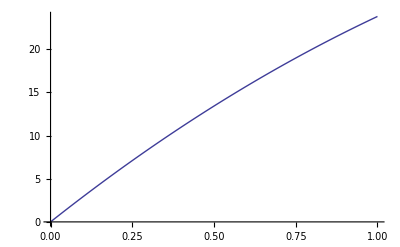

```mathematica
Plot[y[t]/.%[[1]],{t,0,t1}]
```

The plot shows that we have overshot the mark,  reaching somewhat higher than 20m at t=1 s. We need to lower the initial velocity a bit. Of course, we could do this by hand, and by making several attempts eventually we would obtain the required boundary conditions. However, it is easier to automate this process.

Let us define a function yend[v0], the solution at the final time t_1:

```mathematica
yend[v0_]:=( y[t1]/.Sol[v0][[1]]) /; v0∈Reals
```

[Note: the conditional statement  /; v0∈Reals defines the function yend only if its argument is a real number. This conditional did not appear in the first printing of the book. The change is needed for users of Mathematica version 5 or above, but not versions 3 or 4, because later versions have changed the way that FindRoot evaluates functions. Without this change Cell 1.77 will give errors in version 5  or later because FindRoot attempts to evaluate yend with a non-numerical argument.] We can test whether this function is working by trying it out for the case of v0=30m/s:

```mathematica
yend[30]
```

23.8081

This value appears to agree with the  trajectory  plotted  above.

Now we can apply the FindRoot function to solve the equation yend[v0]== y1. To do so, we will need to provide FindRoot with two  initial guesses for v0, since the function ysol[v0] does not have a defined derivative; i.e. ysol'[v0] is not defined (see Sec. 9.11.1).  Since v0=30 almost worked, we'll try two guesses near that:

```mathematica
FindRoot[yend[v0]==y1,{v0,30,29}]
```

{v0→25.9983}

Thus,  a throw of about 26 m/s will hit the mark at 20 m height after one second.  The trajectory is displayed in Cell 1.78 by evaluating Sol at this velocity and plotting the resulting function:

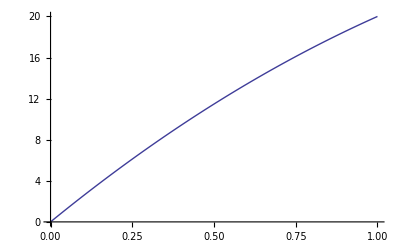

```mathematica
ysol=y/.Sol[v0/.% ][[1]];
Plot[ysol[t],{t,0,t1}]
```

In this example of the shooting method, we found one solution to the boundary-value problem. How do we know that there are no other solutions? We don't . There could be other solutions that would be found if we made different choices for the initial velocity. (Actually, in this particular problem, one can show analytically that the above solution is unique, but for other problems this is not the case; see the exercises.)

This points out a major weakness in the shooting method:

The shooting method only finds one solution at a time. To find a solution, reasonably accurate initial guesses must be made. Thus, it is possible to miss valid solutions to a boundary-value problem when using the shooting method.

Exercises for Sec. 1.5

(1) A thin rod of length L  and mass ρ per unit length  is clamped between two vertical walls at x=0 and x=L. In the absence of gravity, the rod would be horizontal, but in gravity the rod sags with a vertical displacement given by the function y(x). According to the theory of elasticity, the shape of the rod satisfies the following boundary-value problem, assuming that the sag is small: D ∂^4/(∂x^4)y(x)=-ρ g, where g is the acceleration of gravity and D depends on Young's modulus E and the cross-sectional area a of the rod according to D = α E a^2, and where α is a dimensionless constant that depends on the shape of the cross section of the rod. The boundary conditions for a rod clamped at both ends are y(0)=y'(0)=y(L)=y'(L)=0. Solve this problem analytically, and determine the shape y(x) of the rod.  How does the maximum sag scale with the length L of the rod, holding everything else fixed?
[You may wish to compare your results to those obtained in Sec. 9.10, Exercise (5).]

(2) A neutral plasma is a gas of freely moving charged particles, with equal amounts of positive and negative charge. If the plasma encounters a conductor to which a positive voltage is applied, negative plasma charges will be attracted to the conductor and positive charges will be repelled. As a result, an excess negative charge will surround a positively charged conductor. If the applied voltage is not too large, the plasma's net charge density ρ(r) will satisfy a linear law:

ρ(r) = -A ϕ(r)

where ϕ is the electrostatic potential in the plasma at position r, and A is a positive constant that depends on the plasma density and temperature.  The potential satisfies Poisson's equation (1.1.10),  so Eq. (1.5.13) implies a linear PDE for the potential must be solved:

∇^2 ϕ=A/ϵ_o ϕ .

(a) Consider a plasma confined by conducting plates at x=0 and x=L. The plate at x=0  is biased to potential V and the plate at x = L is grounded. Solve analytically the 1-D version of Eq. (1.5.14) , ∂^2/(∂x^2)ϕ=A/ϵ_o ϕ, to obtain ϕ(x) between the plates.

(b) Repeat this solution numerically using the shooting method. Take L=2 and A/ϵ_o  = 1. Plot the analytic and numerical results for ϕ(x).

(3) An artillery sergeant is asked to hit a fixed object at position (x,y)=(d,0) with respect to his cannon. The muzzle velocity of the field piece is fixed at v_o, but the angle θ of the muzzle with respect to the horizontal can be varied.

(a) Solve this boundary-value problem analytically for θ. Show that there are two solutions for θ  if the distance to the object is not too great, but that there is no solution if d exceeds a distance d_max, and find d_max. (Note that the time of impact is unimportant in this problem.)

(b) Create a module that will perform this solution using the shooting method, for given d. Use it to solve the problem where v_o  = 1000 m/s, d = 1 km, and there is linear damping of the shell's velocity, with rate γ = 0.3. Plot the (x,y) trajectory of the shell. By choosing a different initial guess, have the method converge to other solutions, if any; and plot all on the same graph of y vs. x.

(4)(a) A jet aircraft follows a straight trajectory given by R_jet(t)=(v_jet t + x_o, y_o, z_o) where v_jet=250 m/s, x_o=-500 m, y_o=800 m, and z_o=5000 m. An antiaircraft gun at r=0 is trying to shoot the plane down. The muzzle velocity of the gun is v_o=600 m/s.  If the gun fires a shell at t=0, where should it aim (i.e.what is the direction of the initial shell velocity)? Solve the problem analytically (using Mathematica to help with the algebra; the final equation needs to be solved numerically using FindRoot), keeping only the force of gravity on the shell. Plot the trajectory of the shell and the plane using a three-dimensional parametric plot (ParametricPlot3D) up to the instant of impact. Is there more than one solution? [Hint: It is useful to introduce spherical polar angles (θ,ϕ) to describe the direction of the initial shell velocity: v_o=v_o(sin θ cosϕ, sinθ sinϕ, cosθ). See Fig. 1.16.

(b) Repeat the procedure using the shooting method, but now add a frictional deceleration of the form -γ v, where γ=0.075 s^-1.

Fig. 1.16 Spherical polar angles (θ,ϕ) describing the direction of a vector v with respect to fixed axes.

(5) James Bond, mass 85 kg, needs to jump off an overpass onto the bed of a passing truck 12 m below. He is attached to a bungee cord to break his fall, with a nonlinear spring force of -1.1 y^3 newtons, where y is the displacement of Bond from the overpass measured in meters. A positive displacement corresponds to moving down.  By eye he quickly calculates that the truck will be beneath him in 2.1 seconds. He immediately jumps.

(a)Use the shooting method to numerically determine what vertical velocity he must give himself, neglecting friction with the air, so that he lands on the truck at just the right instant. (A positive velocity corresponds to jumping down.) Plot Bond's trajectory. y(t)(Hint: Remember to include gravity, with the right sign!)

(b) Can you find other, less appealing solutions for Bond's initial velocity that involve multiple oscillations at rather high speed?

(6) On January 1, 2001, at 12 noon GMT,  a spacecraft is located 500 km above the earth's surface, on the night side, along the line directly connecting the earth to the sun. The computer controlling  the spacecraft (a HAL9000, of course) has been asked to ensure that the ship will be at the future location of Jupiter exactly three years from this instant. (To be precise, the location is to be 100,000 km on the inboard side of Jupiter on a line toward the sun.) Use a shooting method and the information in Table 1.2 to determine the HAL9000's solution for the required initial velocity of the spacecraft, and plot the trajectory of the craft through the solar system. (Hint: to speed up the orbit integration, keep only the orbits of the earth, Mars, and Jupiter in the simulation. Use the molecular dynamics code developed in Sec. 1.4 to determine the orbits.) The solution is shown graphically in Fig. 1.17 as a plot of the orbits. (The plot can be viewed from different angles by dragging on it with the mouse.)

-Graphics3D-

Fig. 1.17 Solution to Exercise (6).

(7) The temperature of a thin rod of unit length satisfies ⅆ^2 T/ⅆ x^2=(T(x))^4 (in suitably scaled units). [The T^4 term represents heat loss due to radiation, and the ⅆ^2 T/ⅆ x^2term arises from thermal conduction: see Chapter 3.] Find and plot T(x) assuming the ends are held at fixed temperature: T(0)=T(1)=1.

## 1.6 Linear ODEs

1.6.1 The Principle of Superposition

## Linear ODEs of Order N

A linear ODE is distinguished by the following property: the equation is linear in the unknown function; that is, only the first power of this function or its derivatives appear. An Nth-order linear ODE has the form

(ⅆ^N x)/(ⅆ t^N)+ u_(N-1)(t)(ⅆ^(N-1)x)/(ⅆ t^(N-1))+...+ u_1(t)ⅆx/ⅆt + u_o(t)x=f(t).

We have already seen several examples of linear differential equations, such as Eq. (1.1.1) (linear in v),  or Eq. (1.1.6), (linear in x). Another example is the driven damped harmonic oscillator

(ⅆ^2 x)/(ⅆ t^2)+γ ⅆx/ⅆt+ ω_o^2 x=f(t),

where γ and  ω_o^2   are time-independent nonnegative constants.  This equation describes damped harmonic motion with natural frequency ω_o and  damping rate γ, driven by an external force  m f(t)  (where m is the oscillator's mass).

There are many, many other linear ODEs that have physical significance. Linear differential equations play a special role in the physical sciences,  appearing in literally every discipline.  As a consequence, the properties of these equations and their solutions have received considerable attention.

## Linear Differential Operators

An operator is simply a rule that transforms one function into another. An integral is an operator, and so is a square root. Differential operators are combinations of derivatives that act on a given function, transforming it into another function. For example, L̂ f=ⅇ^(ⅆf/ⅆt)  defines a differential operator L̂ (i.e. a rule) that takes the function f(t)  to the function ⅇ^(ⅆf/ⅆt).

Let us define a linear differential operator of Nth-order as

L̂=ⅆ^N/(ⅆ t^N)+ u_(N-1)(t)ⅆ^(N-1)/(ⅆ t^(N-1))+...+ u_1(t)ⅆ/ⅆt + u_o(t).

For the moment, think of this as merely a convenience, so that we can write Eq. (1.6.1) in the compact form L̂ x=f  .

Linear operators have the following two properties:

(1) for any two functions f(t) and g(t), L̂(f+g)=L̂ f+L̂ g.
	 (2) for any function f(t) and any constant C, L̂ (C f)=C L̂ f.

It is easy to see that  the operator in Eq. (1.6.3) satisfies these properties, and so  it is a linear operator. It is also easy to see that the integral of a function is another linear operator (a linear integral operator).  However, the operator defined by L̂ f=ⅇ^(ⅆf/ⅆt)  does not satisfy either property. It is a nonlinear differential operator. For the most part, we will concentrate on the properties of linear operators in this book. Some examples of nonlinear operators with relevance to physics can be found in Chapter 7.

## The Superposition Principle

One important property of linear ODEs is called the principle of superposition. Consider the general solution of Eq. (1.6.1), assuming that the forcing function vanishes: L̂ x = f(t) = 0. In this case the equation is termed homogeneous.

Now, the general solution of the ODE involves N undetermined constants, as discussed in Sec. 1.1. Let us arbitrarily choose any two different sets of values for these constants, and thereby obtain two different possible solutions to the homogeneous equation, x_1(t) and x_2(t) (corresponding to different initial or boundary conditions). Then the principle of superposition states that the linear combination

C_1 x_1(t)+C_2 x_1(t)

is also a solution of the homogeneous ODE (corresponding to some other initial or boundary conditions). This follows directly from the linear nature of the differential equation, as we will now show.

By construction, the functions x_1(t) and x_2(t) have the property that  L̂ x_1=L̂ x_2=0. If we now substitute Eq. (1.6.4) into  Eq. (1.6.1), we obtain

L̂(C_1 x_1+C_2 x_2)=L̂(C_1 x_1)+L̂(C_2 x_2)=C_1 L̂ x_1+C_2 L̂ x_2=0,

verifying our contention that Eq. (1.6.4) satisfies the homogeneous ODE, and proving the principle of superposition.

The Principle of Superposition | 
Ifx_1(t)andx_2(t)both satisfy the homogeneous linear ODEL̂ x=0,then the linear combination C_1 x_1(t)+C_2 x_2(t)
also satisfies this ODE for any value of the constants C_1 andC_2. |  |

1.6.2 The General Solution to the Homogeneous Equation

## Introduction

Let us return now to the discussion surrounding Eq. (1.6.3) regarding the general solution of the homogeneous equation L̂ x=0 .  Rather than choosing only two sets of values for the N undetermined constants, let us choose N different sets of values, so that we obtain N different functions, x_1(t),x_2(t),…,x_N(t).  This means that no one function can be obtained merely as a linear superposition of the others. The functions are linearly independent  of one another.  Then it should be clear that the function obtained by superimposing these functions,

x(t)=C_1 x_1(t)+C_2 x_2(t)+...+C_N x_N(t)

is a form of the general solution of the homogeneous ODE. Recall that the general solution has N undetermined constants that can be used to satisfy any particular initial condition. The fact that the functions x_1(t),x_2(t),…,x_N(t) are linearly independent means that Eq. (1.6.6)  and its derivatives, evaluated at the initial time, span the space of possible initial conditions. By this I mean that any given initial condition can be met by appropriate choice of the constants.  (Note the use of the term span, from linear algebra, denoting a set of vectors  that can be made to sum to any other vector in a given vector space. As we have already mentioned, the connection between linear ODEs and linear algebra will be made clear in the next section.)

We have already seen an example of Eq. (1.6.6): Eq. (1.1.7) shows that the solution of the harmonic oscillator equation is a sum of the linearly independent solutions cos t and sin t. Equation (1.6.6) shows that the general solution of a homogeneous linear ODE can always be written in this way, as a sum of N independent functions each of which satisfy the ODE.

The general solution of a homogeneous linear ODE  L̂ x=0 can be written as a linear combination of N independent solutions to the ODE.

Let's consider possible analytic forms for these N independent solutions in the case that the functions u_n(t) appearing in Eq. (1.6.1) are time-independent constants:

L̂ x=(ⅆ^N x)/(ⅆ t^N)+ u_(N-1)(ⅆ^(N-1)x)/(ⅆ t^(N-1))+...+ u_1 ⅆx/ⅆt + u_o x=f(t).

This important special case occurs, for example, in the driven damped harmonic oscillator, Eq. (1.6.2). We will guess the form x(t)=ⅇ^(s t) for some constant s. Using the fact that

ⅆ^n/(ⅆ t^n)ⅇ^(s t)=s^n ⅇ^(s t) ,

the ODE L̂ x=0becomes a polynomial in s:

(s^N+u_(N-1) s^(N-1)+u_(N-2) s^(N-2)+...+u_1 s+u_o) ⅇ^(s t)=0.

The bracket must be zero, so we are faced with finding the roots of this Nth-order polynomial in  s. Although a general analytic solution cannot be found for N>4, it is well known that there are always N roots (which may be complex), {s_1,s_2,...,s_N} . These N roots supply us with our N independent functions,

x_n(t)=ⅇ^(s_n t),   n=1,2,...,N,

provided that none of the roots are the same. If two of the roots are the same, the roots are said to be degenerate. In this case only N-1 of the solutions have the form of Eq. (1.6.10). The Nth solution remains to be determined.

Let's assume that s_1 = s_2. Then consider any one of the constants in Eq. (1.6.9) to be a variable; take the constant u_o, for example, and replace it with a variable u. Now the roots all become functions of u, and in particular so do our two degenerate roots, s_1 = s_1(u) and s_2 = s_2(u) . Furthermore,  s_1(u_o) = s_2(u_o), but in general for u≠u_o,   s_1(u) ≠ s_2(u). Now let us write u=u_o+ϵ,  and take the limit of the following superposition as ϵ vanishes:

lim_(ϵ→0) 1/ϵ(ⅇ^(s_1(ϵ+u_o) t)-ⅇ^(s_2(ϵ+u_o) t))

According to the superposition principle, this sum is also a perfectly good solution to the equation. Mathematica  can easily carry out the limit, obtaining a finite result:

```mathematica
s2[u0] = s1[u0]=s1;
Factor[Normal[Series[ϵ^-1 (E^(s1[u0+ϵ]t)-E^(s2[u0+ϵ]t)),{ϵ,0,0}]]]
```

ⅇ^(s1 t) t (s1'[u0]-s2'[u0])

The result, t ⅇ^(s_1 t) (neglecting the unimportant multiplicative constant), provides us with the new function necessary to complete the set of N independent solutions. The case of three or more degenerate roots, and the case where the multiplicative constant vanishes, can all be handled easily using similar methods to those detailed here, and will be left for the exercises.

## Different Functional Forms for the General Solution

Often it may happen that the exponential form of the solutions in Eq. (1.6.10) is not the most convenient form for a particular application. For example, for the undamped harmonic oscillator Eq. (1.1.6), the functions obtained via Eq. (1.6.10) are

x_1(t)=ⅇ^(ⅈ ω_o t),  x_2(t)=ⅇ^(-ⅈ ω_o t)

For the damped harmonic oscillator  Eq. (1.6.2), s satisfies a quadratic equation

s^2+γ s+ω_o^2=0,

which has solutions

s_1=-γ/2+ⅈ √(ω_o^2-γ^2/4),
s_2=-γ/2-ⅈ √(ω_o^2-γ^2/4).

These solutions are complex (when ω_o>γ/2), and this can be an inconvenience in certain applications. Fortunately, the superposition principle says that we can replace the functions x_1(t) and x_2(t) with any linear combination of them. For example, the new functions

(x̄)_1(t)=1/2 [x_1(t)+x_2(t)],
(x̄)_2(t)=1/(2ⅈ) [x_1(t)-x_2(t)],

form a useful set of independent solutions for  damped or undamped oscillator problems, since standard trigonometric identities can be used show that these functions are real. For example, for the undamped harmonic oscillator, Eqs. (1.6.12) and (1.6.15) yield

(x̄)_1(t)=cosω_o t,
(x̄)_2(t)=sinω_o t,

which may be recognized as the usual real form for the independent solutions. We can then drop the overbars in Eq. (1.6.16) and treat these functions as our new independent solutions. Similarly, the real solutions to the damped harmonic oscillator equation are

(x̄)_1(t)=ⅇ^(-γ t/2) cos(√(ω_o^2-γ^2/4) t),
(x̄)_2(t)=ⅇ^(-γ t/2) sin(√(ω_o^2-γ^2/4) t).

These solutions are real, assuming that ω_o> γ/2. The solutions decay with time, and oscillate at a frequency less than ω_o due to the drag force on the oscillator.

1.6.3 Linear Differential Operators and Linear Algebra

Consider the following homogeneous linear initial-value problem for the unknown function x(t):

L̂ x=0,x(t_o)=x_o,x'(t_o)=v_o,...,

where L̂  is some linear differential operator. In this section we will show that the function x(t) can be thought of as a vector, and the operator  L̂ can be thought of as a matrix that acts on this vector. We can then apply what we know about linear algebra to understand the behavior of solutions to linear ODEs.

To directly see the connection of Eq. (1.6.18) to linear algebra, consider trying to find a numerical solution to this ODE using Euler's method. We then discretize time, writing t_n= n Δt + t_o. The function x(t) is replaced by a set of values  {x(t_o),x(t_1),x(t_2),...}, which can be thought of as a vector x :

x={x(t_o),x(t_1),x(t_2),...}.

Similarly, the ODE L̂ x=0 becomes a series of linear equations for the components of x, and therefore the operator L̂  becomes a matrix L that acts on the vector x. To see how this works in detail, consider the case of a simple first-order linear homogeneous ODE:

L̂ x=ⅆx/ⅆt+u_o(t)x=0,  x(t_o)=x_o.

Solving this ODE numerically via Euler's method, we replace Eq. (1.6.19) by

x(t_o)=x_o,
x(t_1)-x(t_o)+Δt u_o(t_o)x(t_o)=0,
x(t_2)-x(t_1)+Δt u_o(t_1)x(t_1)=0,...

These linear equations can be replaced by the  matrix equation

(1 | 0 | 0 | 0 | ...
-1+u_o(t_o) Δt | 1 | 0 | 0 | ...
0 | -1+u_o(t_1) Δt | 1 | 0 | ...
0 | 0 | -1+u_o(t_2) Δt | 1 | ...
⋮ | ⋮ | ⋮ | ⋮ | ⋱)·(x(t_o)
x(t_1)
x(t_2)
x(t_3)
   ⋮)
 =(x_o
0
0
0
⋮)

The above matrix is a realization of the matrix L for this simple first-order ODE. All elements above the main diagonal are zero because the recursion relation determines the nth element of x in terms of earlier steps only.  The right-hand side of Eq. (1.6.21) is a vector containing information about the initial condition. We will call this vector x_o={x_o,0,0,...}.

We can easily write the matrix L in terms of a special function called a Kronecker delta function, δ_(n m) .  This function takes two integer arguments, n and m, and is defined as

δ_(n m)={1
0 ,n=m,
,n≠m.

The Kronecker delta function can be thought of as the (n,m) element a matrix whose elements are all zero except along the diagonal n=m, where the elements are equal to one. This is the unit matrix unit, discussed in Sec. 9.5.2. In Mathematica, the function  δ_(n m) is called KroneckerDelta[n,m]. 
	Using the Kronecker delta function, the components L_(m n) of L can be expressed as

L_(n m)=δ_(n m)- δ_(n-1, m)[1-Δt u_o(t_m)]

The matrix can then be created with a Table command:

```mathematica
L=Table[KroneckerDelta[n,m]-KroneckerDelta[n-1,m](1-Δt u[m]),{n,0,3},{m,0,3}];
MatrixForm[L]
```

(1 | 0 | 0 | 0
-1+Δt u[0] | 1 | 0 | 0
0 | -1+Δt u[1] | 1 | 0
0 | 0 | -1+Δt u[2] | 1)

Here we have only constructed four rows of the matrix, for ease of viewing.

Of course, the matrix and vectors of Eq. (1.6.21) are formally infinite–dimensional, but if we content ourselves with determining the solution only up to a finite time t_f = M Δt + t_o, we can make the matrices and vectors M+1-dimensional.

Note that Eq. (1.6.21) is only one of many different possible forms for the matrix equation.  Recall that there are many different schemes for solving an ODE: the Euler method embodied by Eq. (1.6.21) is one, but the predictor-corrector method, for example, would lead to a different matrix L (see the exercises). This uncertainty shouldn’t bother us, since the solution of the matrix equation always leads to an approximate solution to Eq. (1.6.19) that converges to the right solution as Δt → 0,  independent of the particular method used in obtaining the matrix equation.

We can write Eq. (1.6.21) in a more compact form using vector notation:

L·x=x_o.

This matrix equation is a discretized form of the ODE and initial condition,  Eq. (1.6.19). It can be shown that the more general ODE of Eq. (1.6.18) can also be put in this form, although this takes more work. (Some examples can be found in the exercises.) A solution for x  then follows simply by inverting the matrix:

x=L^-1 x_o.

Recall that it is not always possible to find the inverse of a matrix. However, according to Theorem 1.1, the solution to an initial-value problem always exists and is unique, at least for problems that satisfy the strictures of the theorem. For linear problems of this type, the matrix inverse can be taken, and the unique solution given by Eq. (1.6.25) can be found.

We can perform this matrix inversion numerically in Mathematica. But to do so, we must be more specific about the problem we are going to solve.  Lets take the case t_o=0 , x_o = 1, and u_o(t) = 1, a constant damping rate. The equation we solve is then ⅆx/ⅆt = -x, x(0)=1. Then the analytic  solution to Eq. (1.6.19) is a simple exponential decay: x(t)=exp(-t).

To do the problem using matrix inversion, we choose a step size , say, Δt=0.05, and solve the problem only up to a finite time t_f = 2. This implies that the dimension M of the vector x_o is 2/0.05 + 1 = 41, (the "+1" is necessary because t=0 corresponds to the first element of x_o), and the matrix L is 41 by 41.  The following Mathematica statements set up the vector x_o and the matrix L:

```mathematica
Δt = 0.05;u[n_] = 1; M=40;
x0 = Table[0,{n,0,M}];
x0[[1]] = 1;
L=Table[KroneckerDelta[n,m]-KroneckerDelta[n-1,m](1-Δt u[m]),{n,0,M},{m,0,M}];
```

We then solve for x using Eq. (1.6.25), and create a data list sol consisting of times and positions {t_n,x_n}:

```mathematica
x=Inverse[L].x0;
sol = Table[{n Δt,x[[n+1]]},{n,0,M}];
```

This solution can be plotted and compared with exp(-t) (see Cell 1.83), showing good agreement (which could be further improved by taking a smaller step size and increasing the dimension M of the system).

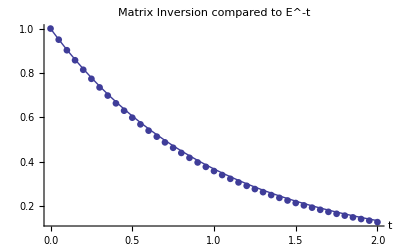

```mathematica
a=ListPlot[sol,PlotStyle->PointSize[0.012]];
b=Plot[E^-t,{t,0,2}];
Show[a,b,PlotLabel->"Matrix Inversion compared to E^-t",AxesLabel->{"t",""}]
```

Note that the matrix-inverse method of solution, outlined above,  is equivalent to the recursive solution of Eq.  (1.6.20). In fact,  performing the recursion in Eq. (1.6.20) can be thought of as just a way of performing the operations of taking the matrix inverse and applying the inverse to x_o, so little is gained in any practical sense from using Eq. (1.6.25) rather than Eq. (1.6.20).

The matrix inverse method is really most useful in solving linear boundary-value problems, because matrix inversion solves the problem in a single step.  This compares favorably with the shooting method for boundary-value problems (discussed in Sec. 1.5.2) , which is an iterative process that requires several steps and an initial guess to find the solution.

Finally, we note the following: we have seen that a matrix L can be connected to any linear differential operator L̂ , and the inverse of the matrix, L^-1,  is useful in finding a solution to ODEs involving L̂ . Therefore, it may  be useful to think about the inverse of the operator itself, which we might write as  (L̂)^-1. In fact, we will see in Chapter 2 that the inverse of a linear differential operator can be defined, that its discretized form is L^-1, and that this operator inverse is connected to the idea of a Green’s function.

1.6.4 Inhomogeneous Linear ODEs

## Homogeneous and Particular Solutions

In the preceding sections, we discussed solutions x(t) to the homogeneous linear ODE  for some linear differential operator L̂ .  Let us now consider the case of an inhomogeneous linear ODE,

L̂ x=f.

We will examine the general solution of this problem, so that we do not have to specify boundary or initial conditions. Using the superposition principle, we write the general solution as a linear combination of two functions:

x(t)=x_h(t)+x_p(t),

where x_h(t) is the general solution to the homogeneous problem, satisfying

L̂ x_h=0,

and where x_p(t) is any solution to the inhomogeneous problem, satisfying

L̂ x_p=f.

The function x_h is called the homogeneous solution, and the function x_p is called a particular solution.

Acting on Eq. (1.6.27) with L̂, it is clear that x(t)  satisfies Eq. (1.6.26). It is also clear that Eq. (1.6.28) is the general solution of Eq. (1.6.26), since x_h(t) contains all of the undetermined constants necessary to satisfy any given set of boundary or initial conditions.

We have already discussed how to find  the homogeneous solution x_h(t), in Sec. 1.6.2 . The problem then comes down to finding a particular solution x_p(t)  to the inhomogeneous problem.  This is actually rather nontrivial, and a complete and general answer will not be obtained until the end of Chapter 2. We will take the problem in steps of increasing difficulty.

## Method of Undetermined Coefficients

As a first step to finding a particular solution, we will consider the case where the ODE has constant coefficients; i.e., the functions u_n(t) appearing in Eq. (1.6.1) are time-independent constants, so that the Nth-order ODE takes the form of Eq. (1.6.7). Also, we will assume that the forcing function f(t) is of a very simple analytic form. With these assumptions,  an analytic  solution for x_p(t)  can be found simply by guessing a form for the solution. This is called the "method of undetermined coefficients" in elementary texts on ODEs.

Take, for example, the simple case of a linearly increasing force,

f(t)=a+b t.

For the response to this force, let's try the same form back again:

x_p(t)=A + B t,

where A and B are undetermined coefficients. Acting on this guess with L̂  yields

L̂ x_p=u_o(A+B t)+u_1 B ,

which is of the same form as f, provided that we now choose values for A and B correctly so as to satisfy Eq. (1.6.7):

u_o A+u_1 B=a,   u_o B=b.

According to Eq. (1.6.31), one way that the system can respond to a linearly increasing force is for the amplitude to increase linearly as well: as you push harder on a spring, it stretches further.  But this is only one possible solution; the spring could also oscillate. In fact, we know that the general solution to this problem is

x(t)=x_h(t)+A + B t.

The oscillations are contained in the homogeneous solution x_h(t), and their amplitude is set by the initial or boundary conditions.

## Response to Sinusoidal Forcing

There are many other analytically-tractable forcing functions that we could consider. Of course, Mathematica could find such solutions for us, using DSolve.  However, there is one more case that we will solve in detail by hand, because it  will turn out to be  of great importance to our future work:  the case of an oscillating  force of the form

f(t)=f_o cosω t.

A particular solution for this type of force can be found using the guess

x_p(t)=A cosω t+ B sinω t,

where the constants A and B remain to be determined. In other words, the system responds to the oscillatory forcing with an oscillation of the same frequency.  If we substitute this into Eq. (1.6.7)  we obtain, after some work,

L̂ x_p=cos(ω t) ∑_(n=0)^(N/2) (A (u_(2 n)(-ω^2))^n+B ω (u_(2 n+1)(-ω^2))^n) +   sin(ω t) ∑_(n=0)^(N/2) (B (u_(2 n)(-ω^2))^n-A ω (u_(2 n+1)(-ω^2))^n).

This equation can be solved by choosing A and B so that the coefficient of sinω t  vanishes and the coefficient of cosω t equals f_o.

A simpler alternative method of solution for this problem employs complex notation. We replace Eq. (1.6.35) by

f(t)=Re f_o ⅇ^(-ⅈ ω t)

and we now try the form

x_p(t)=Re C ⅇ^(-ⅈ ω t)

where C =|C| ⅇ^(ⅈ ϕ) is a complex number. The magnitude |C| is the amplitude of the oscillation, and the argument ϕ is the phase of the oscillation with respect to the applied forcing.  Using amplitude and phase notation, Eq. (1.6.39) can be written as

x_p(t)=|C|cos(ω t -ϕ) =|C|cosϕ cosω t+|C|sinϕ sinω t.

By comparing Eq. (1.6.40) to Eq. (1.6.36)  we can make the identifications A=|C|cosϕ  and B=|C|sinϕ .

The solution for x_p(t)  can again be found by substituting Eq. (1.6.39) into Eq. (1.6.7):

L̂ x_p=Re C L̂  ⅇ^(-ⅈ ω t)=Re f_o  ⅇ^(-ⅈ ω t) ,

where we have assumed that the coefficients u_n in  Eq. (1.6.7) are real in order to take the operation Re through L̂  .  Now, rather than solving only for the real part, we will solve the full complex equation. (If the full complex equation is satisfied, the real part will also be satisfied.) Also, we will use the fact that

ⅆ^n/(ⅆ t^n)ⅇ^(-ⅈ ω t)=(-ⅈ ω)^n ⅇ^(-ⅈ ω t),

so that Eq. (1.6.41) becomes

C ⅇ^(-ⅈ ω t)∑_(n=0)^N (-ⅈ ω)^n u_n=f_o ⅇ^(-ⅈ ω t).

Dividing through by the sum and using Eq. (1.6.39) allows us to write x_p(t) in the following elegant form:

x_p(t)=Re( f_o/(∑_(n=0)^N (-ⅈ ω)^n u_n)ⅇ^(-ⅈ ω t))

In future chapters we will find that complex notation often simplifies algebraic expressions involving trigonometric functions.
	Let us use Eq. (1.6.44) to explore the particular solution for the forced damped oscillator, Eq. (1.6.2). For the choice of u_n's corresponding to this ODE, Eq. (1.6.44) becomes

x_p(t)=Re( f_o/(-ω^2-ⅈ ω γ +ω_o^2)ⅇ^(-ⅈ ω t))

This particular solution oscillates at constant amplitude, and with the same frequency as the forcing. Since the homogeneous solutions decay with time [see Eq. (1.6.17)], Eq. (1.6.45) represents the form of the solution at times large compared to 1/γ. At such large times, the oscillator has  'forgotten' its initial conditions;  every initial condition approaches Eq. (1.6.45).  The convergence of different solutions can be seen directly in Fig. 1.18, which displays the time evolution of three different initial conditions. All three solutions converge to Eq. (1.6.45).

Fig. 1.18 Three solutions to the driven damped oscillator equation x''+x'+2x=cos3 t.

The loss of memory of initial conditions at long times is a general feature of linear driven damped systems. Nonlinear driven damped systems, such as the van der Pol oscillator [Eq. (1.2.20)] with a driving term added, also display loss of memory of initial conditions; but initial conditions do not necessarily collapse onto a single trajectory as in Fig. 1.18. For instance, orbits can collapse onto a strange attractor, and subsequently wander chaotically across the surface of this attractor. A detailed analysis of the complex chaotic behavior of nonlinear driven damped systems is beyond the scope of this introductory text; see Ott (1993),  for a discussion of this subject.

## Resonance

The particular solution to the driven damped oscillator equation has an amplitude that depends on the frequency ω at which the system is driven.  According to Eq. (1.6.45), this complex amplitude is C =f_o/(-ω^2-ⅈ ω γ +ω_o^2) . Plots of the magnitude and phase of C/f_o are shown in Fig. 1.19 as a function of  ω.

Fig. 1.19 : Magnitude (thick line) and phase (thin line) of the amplitude of the particular solution to the driven damped oscillator:
(a) heavy damping, γ/ω_o=0.7; (b) light damping, γ/ω_o=0.1. Also shown is the location of the peak amplitude, ω=√(ω_o^2-γ^2/2) (dashed line).

These plots show that a resonance occurs when the driving frequency ω is close to the natural frequency ω_o: the amplitude of oscillation has a maximum near ω_o, and the phase of the oscillation changes from a value near zero (the oscillation is in phase with the driving force) to one near π (the oscillation has the opposite sign to the driving force). The resonance becomes sharper as the damping γ becomes weaker. The frequency at which the amplitude is maximized can be easily shown to be equal to √(ω_o^2-γ^2/2)(see the exercises). Note that this is not the same as the frequency  of unforced oscillations in a damped oscillator, √(ω_o^2-γ^2/4) [see Eq. (1.6.17)].

When the damping equals zero exactly, the undamped oscillator exhibits an exact resonance when driven at ω=ω_o. Here the amplitude C becomes infinite, and therefore the form of the solution, Eq. (1.6.45), is no-longer valid.

One way to find the solution at an exact resonance is to use DSolve:

```mathematica
Clear[x];
Expand[FullSimplify[x[t]/.DSolve[x''[t]+Subscript[ω, o]^2 x[t] ==Subscript[f, o]  Cos[Subscript[ω, o] t],x[t],t][[1]]]]
```

C[2] Cos[t ω_o]+C[1] Sin[t ω_o]+(Cos[t ω_o] f_o)/(4 ω_o^2)+(t Sin[t ω_o] f_o)/(2 ω_o)

In addition to the usual cosine and sine terms, there is a new term proportional to t sin ω_o t. This term is an oscillation that grows in amplitude over time. At an exact (i.e. undamped, linear) resonance, the force is always in phase with the oscillation, adding energy to the motion in every cycle. Since this energy is not dissipated by damping, the oscillation increases without bound.  Of course, in any real oscillator, some form of damping or nonlinearity will eventually come into play, stopping the growth of the oscillation.

In later chapters we will run across examples of other  linear ODEs that exhibit exact resonance when driven at a natural frequency of the system . In each case, the response grows with time, and therefore must be treated as a special case for which Eq. (1.6.44) does not apply.  The simplest approach is to apply DSolve or the method of undetermined coefficients for the case of resonance, and to use Eq. (1.6.44) otherwise.

Nevertheless, it is useful to understand mathematically how this  resonant behavior arises. Consider an undamped oscillator driven at a frequency just off resonance, with forcing f(t) = f_o cos[(ω_o- ϵ)t]. Then the particular solution is given by Eq. (1.6.45) with γ=0:

x_p(t) = f_o cos[(ω_o- ϵ)t]/(2ω_o ϵ-ϵ^2) .

This oscillation has very large amplitude, approaching infinity as ϵ→ 0. However, consider a different particular solution; one that is chosen to be zero initially. Such a solution can be obtained by adding in a homogeneous solution  to the oscillator equation. One choice for the homogeneous solution is simply A cos ω_o t, with the appropriate choice of the constant A  so that the solution is zero at t=0:

x_p(t) =f_o/(2ω_o ϵ-ϵ^2)(cos[(ω_o- ϵ)t] - cos ω_o t )

The two cosine  functions are at nearly the same frequency, and therefore exhibit the phenomenon of beats, as shown in Cell 1.85 (for the case ω_o=1):

```mathematica
Manipulate[Plot[Cos[(1-ϵ) t]-Cos[t],{t,0,200}],{{ϵ,.1},0.001,.1,Appearance->"Open"}]
```

Oscillations grow for a time, then decay due to the interference between the two cosine functions. The smaller the frequency difference between the two cosine oscillations, the longer the beats become. (Try changing the frequency difference ϵ in Cell 1.85.) Finally, in the limit as the difference ϵ →  0, the length of time between beats goes to infinity, and the initial linear growth in amplitude of the oscillation continues indefinitely; the oscillation grows without bound.  To see this from Eq. (1.6.47) mathematically, we can take a limit (see Cell 1.86).

```mathematica
Limit[Subscript[f, o]/(2 Subscript[ω, o] ϵ - ϵ^2)(Cos[(Subscript[ω, o]-ϵ)t]-Cos[Subscript[ω, o] t]),ϵ->0]
```

(t Sin[t ω_o] f_o)/(2 ω_o)

This limit reproduces the linear amplitude growth observed in the general solution of the undamped oscillator found previously using DSolve.

The examples we have seen so far in this section have all involved simple forcing functions. In the next chapter we will learn how to deal with general f(t), and in the process develop an understanding of Fourier series and integrals.

Exercises for Sec. 1.6

(1) In the introduction to Sec. 1.6.1, we presented an operator L̂ defined by L̂ f=ⅇ^(ⅆf/ⅆt),  as an example of a nonlinear operator. On the other hand, consider the operator defined by L̂ f=ⅇ^(ⅆ/ⅆt)f. Here, ⅇ^(ⅆ/ⅆt)=1+ⅆ/ⅆt+1/(2!)(ⅆ/ⅆt)^2+1/(3!)(ⅆ/ⅆt)^3 +... .  Is this operator linear or nonlinear? Find and plot the action of both operators on f(t)=sin t, on 0<t<2π . (Hint: The infinite series can be summed analytically.)

(2) Find, by hand, a complete set of independent solutions to the following linear homogeneous ODEs. (You may check your results using Mathematica, of course.):

(a) x''''+2 x'''+3 x''+2 x'+2x=0 .

(b) x''''+6 x'''+38 x''+112 x'+104x=0 .

(c)  x'''-3 x''+3 x'-x=0.

(d)  x''=2(y-x)-x',  y''=2(x-y)-y'.

(3) Use the matrix inversion technique to solve the following ODE numerically:

L̂ v=ⅆv/ⅆt+t v(t)=0, v(0)=1.

Use the Euler method form, Eq. (1.6.23), for the finite-differenced version of the operator L̂ on the range 0<t<3, with Δt = 0.05.  Plot the solution on this time interval, and compare it with the exact solution found with Mathematica.

(4) A finite-difference method for second-order ODEs was discussed in Sec. 1.4; see Eqs. (1.4.27) and (1.4.28). Using this method, finite-difference Airy's equation

(ⅆ^2 x)/(ⅆ t^2)=-t x(t),

with initial conditions x(-1)=1,x'(-1)=0. Write the ODE and initial conditions as a matrix equation of the form (1.6.24). Solve the ODE by matrix inversion, taking Δt = 0.1, for -1<t<5, and plot the result along with the analytic result found from Mathematica using DSolve.

(5) For the following general first-order linear ODE, find the matrix L that corresponds to the second-order predictor-corrector method, and write out the first four rows of L:

ⅆx/ⅆt + u_o(t) x = 0.

Use this matrix to solve the initial-value problem where u_o(t) = t/(1+t^2) and x(0)=1, for 0<t<5 taking Δt=0.1. Plot x(t) and on the same plot, compare it with the exact solution found using DSolve.

(6) Add the following forcing functions to the right-hand side of the problems listed in Exercise (2), and solve for a particular solution by hand using the method of undetermined coefficients. (You can use Mathematica to help with the algebra, and to check your answers.):

(a) f(t) = sin(t) to Exercise (2)(a) and (b)

(b) f(t) = t^3 to Exercise (2)(c)

(c) x''=2(y-x)-x', y''=2(x-y)+cos 2t.

(7)(a) Find the potential ϕ(x) between two parallel conducting plates located at x=0 and at x=L. The potential on the left plate is V_1, and that on the right plate is V_2. There is a charge density between the plates of the form ρ=ρ_o cos k x. The potential satisfies ⅆ^2 ϕ/ⅆ x^2=-ρ/ϵ_o.

(b) Discuss the behavior of the answer from part a)  for the case of constant charge density, k=0.

(8) Consider an LRC circuit driven by an oscillating voltage V(t) = V_o cosωt.  The charge on the capacitor satisfies Eq. (1.3.3). The homogeneous solution was found in Sec. 1.3, Exercise (3).

(a) Find a particular solution for the charge using the method of complex exponentials, Q_p(t)=Re(Q_o ⅇ^(-i ω t))

(b) For V_o = 1 Volt, R = 2 ohms, C = 100 pico-farads and L = 2 × 10^-3 Henry, find the resonant frequency of the circuit. Plot the amplitude |Q_o| and phase ϕ of the particular solution vs. ω over a range of ω from zero to twice the resonant frequency.

(9) A damped linear oscillator has mass m and has a Hooke's law force constant k and a linear damping force of the form F_d = -m γ v(t). The oscillator is driven by an external periodic force of the form F_ext(t) = F_o sinωt.

(a) Find a particular solution in complex exponential form, x_p(t)=Re(C ⅇ^(-i ω t))

(b) The rate of work done by the external force on the mass is ⅆ W_ext/ⅆt=F_ext(t)v(t) . Using the particular solution v_p(t) from part (a), find a (time-independent) expression for ⟨ⅆ W_ext/ⅆt⟩, the average rate of work done on the mass, averaged over an oscillation period 2π/ω.  .
Hint: Be careful! When evaluating the work the real solution for v_p(t) must be used. Use Mathematica to help do the required time integration over a period of the oscillation.)

(c) According to part (b) work is being done on the mass by the external force, but according to part (a) its amplitude of oscillation is not increasing.  Where is the energy going?

(d) Work is done by the damping force F_d on the mass m at the rate ⅆ W_d/ⅆt=F_d(t)v(t). The work is negative, indicating that energy flows from the mass into the damper. What happens to this energy? Using the particular solution from part (a) for v(t), show that  <ⅆ W_d/ⅆt> + <ⅆ W_ext/ⅆt> =0.

(10) Find the length of time between beats in the function cos[(ω_o-ϵ) t] - cos ω_o t  (i.e. the time between maxima in the envelope of the oscillation.) Show that this time goes to infinity as ϵ→ 0 . (Hint: Write this combination as the real part of complex exponential functions, and go on from there.)

(11) Show that the response of a damped oscillator to a  harmonic driving force at frequency ω, Eq. (1.6.45),  has a maximum amplitude of oscillation when ω=√(ω_o^2-γ^2/2).

## References

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations (John Wiley and Sons, New York, 1969).

G.W. Marcy and R. P. Butler, Detection of extrasolar giant planets, Ann. Rev. Astron. and Astroph. 36, 57 (1998).

W. H. Press, S. A. Teukolsky , W. T. Vetterling, and B. P. Flannery, Numerical Recipes (Cambridge University Press,  Cambridge, 1986).

E. Ott, Chaos in Dynamical Systems (Cambridge University Press, Cambridge, 1993).

A. J. Lichtenberg and M. A. Lieberman, Regular and Chaotic Dynamics, 2nd ed. (Springer-Verlag, New York, 1992).